## Cylindrical rod

### Beautiful output

```mathematica
ForPrint={
Derivative[i__][f_][x__]:> Subscript[f,Row@Flatten@MapThread[Table,{{x},{i}}]],
U[x__]:>U, V[x__]:>V,U0[x__]->Subscript[U, 0],V0[x__]-> Subscript[V, 0],U1[x__]->Subscript[U, 1],V1[x__]-> Subscript[V, 1],
U2[x__]->Subscript[U, 2],V2[x__]-> Subscript[V, 2],V3[x__]->Subscript[V, 3],U4[x__]->Subscript[U, 4]};
ForPrint2={U0->Subscript[U, 0],V0-> Subscript[V, 0],U1->Subscript[U, 1],V1-> Subscript[V, 1],U2->Subscript[U, 2],V2-> Subscript[V, 2],V3->Subscript[V, 3],U4->Subscript[U, 4]};
ForLatex={
Subscript[Subscript[f_,n_],Row[{a__}]]->Subscript[f,Flatten[{n,a}]/.List->Sequence],
Subscript[f_,Row[{a__}]]->Subscript[f,Flatten[{a}]/.List->Sequence]};
```

### Elasticity

Notation:
Displace - displacement vector
Deform - gradient of displacement vector in cylindrical coordinates
SGr - Green strain tensor
Pot - potential energy density
P - first Piola-Kirchhoff stress tensor

```mathematica
ClearAll[U,V,W,λ,μ];
Displace={U[x,r,t],V[x,r,t],0};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
```

```mathematica
Inv1[tensor_]:=Tr[tensor];
Inv2[tensor_]:=((Tr[tensor])^2-Tr[tensor.Transpose[tensor]])/2;
Inv3[tensor_]:=Det[tensor];

StrainGreen[mode_]:=Module[{SGr},
SGr=(Transpose[Deform]+Deform)/2;
If[mode=="nonlinear",SGr=SGr+(Transpose[Deform].Deform)/2];
SGrTemplate={
{Subscript[SG, xx],Subscript[SG, xy],Subscript[SG, xz]},
{Subscript[SG, yx],Subscript[SG, yy],Subscript[SG, yz]},
{Subscript[SG, zx],Subscript[SG, zy],Subscript[SG, zz]}};
SGrSubst={ 
Subscript[SG, xx]->SGr⟦1,1⟧,Subscript[SG, xy]->SGr⟦1,2⟧,Subscript[SG, xz]->SGr⟦1,3⟧,
Subscript[SG, yx]->SGr⟦2,1⟧,Subscript[SG, yy]->SGr⟦2,2⟧,Subscript[SG, yz]->SGr⟦2,3⟧,
Subscript[SG, zx]->SGr⟦3,1⟧,Subscript[SG, zy]->SGr⟦3,2⟧,Subscript[SG, zz]->SGr⟦3,3⟧};
I1 = Inv1[SGrTemplate];
I2 = Inv2[SGrTemplate];
I3 = Inv3[SGrTemplate];
SGr];

PotEnergy[mode_]:=Module[{Pot},
Pot=(λ+2 μ)/2 I1^2-2 μ I2;
If[mode=="nonlinear",
Pot=Pot+(l+2 m)/3 I1^3-2 m I1 I2+n I3];
Pot/.SGrSubst];

Poila[mode_]:=Module[{P,Pot},
If[mode=="linear",P=λ Inv1[SGr]IdentityMatrix[3]+2μ SGr//Simplify];
If[mode=="nonlinear",
Pot=Pot=(λ+2 μ)/2 I1^2-2 μ I2+(l+2 m)/3 I1^3-2 m I1 I2+n I3;
P=(IdentityMatrix[3]+Deform).{
{D[Pot, Subscript[SG, xx]],D[Pot, Subscript[SG, xy]],D[Pot, Subscript[SG, xz]]},
{D[Pot, Subscript[SG, yx]],D[Pot, Subscript[SG, yy]],D[Pot, Subscript[SG, yz]]},
{D[Pot, Subscript[SG, zx]],D[Pot, Subscript[SG, zy]],D[Pot, Subscript[SG, zz]]}}/.SGrSubst ];
P];
```

```mathematica
mode="nonlinear";
SGr=StrainGreen[mode];
Pot=PotEnergy[mode];
P=Poila[mode];
```

### Scaling

```mathematica
Scales={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k) s^k,
U[x__]->ε L U[x],V[x__]->ε L V[x],Power[r,n_]->( L r)^n};
Scales2={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k)s^k,
U[x__]->ε L U[x],V[x__]->ε L V[x],r->L r};
```

### Pre-stress solution

```mathematica
USeries[x_,r_,t_]=γ x;
VSeries[x_,r_,t_]=(V10(*+ε V11*))r;
```

#### Equations

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/δ/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Series[ndEq1,{ε,0,1}]//Simplify
ndEq2//Simplify
```

0

0

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2]
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
Series[ndP⟦2,2⟧/ε,{ε,0,1}]//Simplify
ndP⟦2,1⟧
```

O[ε]^2

0

```mathematica
V[x,r,t]
```

r (V10+V11 ε)

```mathematica
V10=-λ/(2(λ+μ))γ+FV1 ε;
```

```mathematica
FV1=-(γ^2 (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2))/(8 (λ+μ)^3);
```

### 1st Method: nonlinear dimensionless equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2+U4[x,t] r^4;
VSeries[x_,r_,t_]=V1[x,t]r+V3[x,t] r^3+V5[x,t] r^5;
```

Pre-stress:

```mathematica
ClearAll[V1,FV1];
USeries[x_,r_,t_]=γ x+U0[x,t]+U2[x,t] r^2 δ^2+U4[x,t] δ^4 r^4;
VSeries[x_,r_,t_]=((-γ λ/2 /(λ+μ)-γ^2 ε (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2)/8 /(λ+μ)^3) r
+V1[x,t]r+V3[x,t] δ^2 r^3+V5[x,t] δ^4 r^5);
```

#### Equations

```mathematica
ClearAll[U,V];
(* Note: to calculate the "normal" divergence, tensor has to be transposed before application of Div[],
however here we calculate divergence of a two-point tensor with respect to the reference coordinates,
which results in transposed  tensor, hence we don't need transposing here. *)
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];

Print["Equation 1:"]
cl=CoefficientList[ndEq1,{ε,r}];
ndEq1red=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧r^2;
Series[ndEq1red,{r,0,2},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify

Print["Equation 2:"]
cl=CoefficientList[ndEq2,{ε,r},{2,5}];
ndEq2red=cl⟦1+0,1+1⟧r+cl⟦1+1,1+1⟧r ε+cl⟦1+0,1+3⟧r^3;
Series[ndEq2red,{r,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

Equation 1:

((-4 μ U_2-2 (λ+μ) V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x))+(2 U_2 ((-4 m+n-4 (λ+μ)) V_1-2 (m+λ+2 μ) U_(0,x))-((8 l+n+2 (λ+μ)) V_1+2 (2 l+m+λ+μ) U_(0,x)) V_(1,x)-(2 (2 l+λ) V_1+(2 l+4 m+3 λ+6 μ) U_(0,x)) U_(0,x,x)) ε+O[ε]^2)+(-16 μ U_4-4 (λ+μ) V_(3,x)+s^2 ρ U_(2,t,t)-(λ+2 μ) U_(2,x,x)) r^2+O[r]^3

Equation 2:

((-8 (λ+2 μ) V_3-2 (λ+μ) U_(2,x)+s^2 ρ V_(1,t,t)-μ V_(1,x,x))+(-(4 m+n+4 λ+12 μ) U_2^2-16 l V_3 U_(0,x)-8 λ V_3 U_(0,x)-4 l U_(0,x) U_(2,x)-2 m U_(0,x) U_(2,x)-2 λ U_(0,x) U_(2,x)-2 μ U_(0,x) U_(2,x)-3 m V_(1,x)^2+1/4 n V_(1,x)^2-3 λ V_(1,x)^2-5 μ V_(1,x)^2-m V_(1,x) U_(0,x,x)-λ V_(1,x) U_(0,x,x)-2 μ V_(1,x) U_(0,x,x)-2 (m+μ) U_2 (4 V_(1,x)+U_(0,x,x))-(m+λ+2 μ) U_(0,x) V_(1,x,x)+1/2 V_1 (-32 (2 (l+m+λ)+3 μ) V_3-2 (8 l+n+2 (λ+μ)) U_(2,x)+(-4 m+n-4 (λ+μ)) V_(1,x,x))) ε+O[ε]^2) r+(-4 (λ+μ) U_(4,x)+s^2 ρ V_(3,t,t)-μ V_(3,x,x)-24 (λ+2 μ) V5[x,t]) r^3+O[r]^4

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2]
bound={r->δ};
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];

Print["P_rr = "]
cl=CoefficientList[(ndP⟦2,2⟧/.bound)/ε-μ(3λ+2μ)/(λ+μ) S[x,t],{ε,δ}];
ndPrrRed=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
Series[ndPrrRed,{δ,0,2},{ε,0,1}]//FullSimplify

Print["P_xr = "]
cl=CoefficientList[(ndP⟦1,2⟧/.bound)/ε/δ-μ(3λ+2μ)/(λ+μ) T[x,t],{ε,δ}];
ndPrxRed=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
Series[ndPrxRed,{δ,0,2},{ε,0,1}]//FullSimplify
```

P_rr =

((-(μ (3 λ+2 μ) S[x,t])/(λ+μ)+2 (λ+μ) V1[x,t]+λ U0^(1,0)[x,t])+((4 l+2 m+3 (λ+μ)) V1[x,t]^2+(4 l-2 m+n+λ) V1[x,t] U0^(1,0)[x,t]+1/2 (2 l+λ) (U0^(1,0)[x,t])^2) ε+O[ε]^2)+((4 λ+6 μ) V3[x,t]+λ U2^(1,0)[x,t]) δ^2+O[δ]^3

P_xr =

(μ (-((3 λ+2 μ) T[x,t])/(λ+μ)+2 U2[x,t]+V1^(1,0)[x,t])+(U2[x,t] ((4 m-n+4 (λ+μ)) V1[x,t]+2 (m+λ+2 μ) U0^(1,0)[x,t])+1/2 ((4 m-n+2 μ) V1[x,t]+2 (m+μ) U0^(1,0)[x,t]) V1^(1,0)[x,t]) ε+O[ε]^2)+μ (4 U4[x,t]+V3^(1,0)[x,t]) δ^2+O[δ]^3

```mathematica
(* Reduction of other components of the stress tensor for plasticity analysis *)
cl=CoefficientList[(ndP⟦1,1⟧/.r->δ)/ε,{ε,δ},{2,4}];
ndPxxRed=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
```

```mathematica
cl=CoefficientList[(ndP⟦1,2⟧/.r->δ)/ε/δ,{ε,δ},{2,4}];
ndPxrRed=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
```

#### High order displacements (U2, V3, U4)

```mathematica
ClearAll[U4,FU4]
cl=CoefficientList[ndEq1red,{r,ε}];
U4[x_,t_]=Solve[cl⟦1+2,1+0⟧==0,U4[x,t]]⟦1,1,2⟧+ε FU4[x,t];
cl=CoefficientList[ndEq1red,{r,ε}];
FU4[x_,t_]=Solve[cl⟦1+2,1+1⟧==0,FU4[x,t]]⟦1,1,2⟧//Simplify;
(cl⟦1+2,1+0⟧==0//Simplify)&&(cl⟦1+2,1+1⟧==0//Simplify)
(* additional test *)
U4[x,t]-(s^2 ρ Derivative[0,2][U2][x,t]-4 (λ+μ) Derivative[1,0][V3][x,t]-(λ+2 μ) Derivative[2,0][U2][x,t])/(16 μ)==0//Simplify
```

True

True

```mathematica
ClearAll[V3,FV3]
cl=CoefficientList[ndEq2red,{r,ε}];
V3[x_,t_]=Solve[cl⟦1+1,1+0⟧==0,V3[x,t]]⟦1,1,2⟧+ε FV3[x,t];
cl=CoefficientList[ndEq2red,{r,ε}];
FV3[x_,t_]=Solve[cl⟦1+1,1+1⟧==0,FV3[x,t]]⟦1,1,2⟧//Simplify;
(cl⟦1+1,1+0⟧==0//Simplify)&&(cl⟦1+1,1+1⟧==0//Simplify)
```

True

```mathematica
CoefficientList[V3[x,t],ε]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

{(-2 (λ+μ) U_(2,x)+s^2 ρ V_(1,t,t)-μ V_(1,x,x))/(8 (λ+2 μ)),-1/(32 (λ+2 μ)^2)(4 (λ+2 μ) (4 m+n+4 (λ+3 μ)) U_2^2+8 m λ U_(0,x) U_(2,x)+16 l μ U_(0,x) U_(2,x)+16 m μ U_(0,x) U_(2,x)+16 λ μ U_(0,x) U_(2,x)+16 μ^2 U_(0,x) U_(2,x)+12 m λ V_(1,x)^2-n λ V_(1,x)^2+12 λ^2 V_(1,x)^2+24 m μ V_(1,x)^2-2 n μ V_(1,x)^2+44 λ μ V_(1,x)^2+40 μ^2 V_(1,x)^2+4 m λ V_(1,x) U_(0,x,x)+4 λ^2 V_(1,x) U_(0,x,x)+8 m μ V_(1,x) U_(0,x,x)+16 λ μ V_(1,x) U_(0,x,x)+16 μ^2 V_(1,x) U_(0,x,x)+8 (m+μ) (λ+2 μ) U_2 (4 V_(1,x)+U_(0,x,x))+8 l s^2 ρ U_(0,x) V_(1,t,t)+4 s^2 λ ρ U_(0,x) V_(1,t,t)+4 (λ (m+λ)+(-2 l+2 m+3 λ) μ+4 μ^2) U_(0,x) V_(1,x,x)-2 V_1 (2 (-8 l μ+8 m (λ+μ)-n (λ+2 μ)+2 (λ+μ) (3 λ+4 μ)) U_(2,x)-4 s^2 (2 (l+m+λ)+3 μ) ρ V_(1,t,t)+(-4 m λ+(n-4 λ) λ+2 (4 l+n-2 λ) μ+4 μ^2) V_(1,x,x)))}

```mathematica
ClearAll[U2,FU2]
cl=CoefficientList[ndEq1red,{r,ε}];
U2[x_,t_]=Solve[cl⟦1+0,1+0⟧==0,U2[x,t]]⟦1,1,2⟧+ε FU2[x,t];
cl=CoefficientList[ndEq1red,{r,ε}];
(*(cl⟦1+0,1+0⟧==0//Simplify)&&(cl⟦1+0,1+1⟧==0//Simplify)*)
FU2[x_,t_]=Solve[cl⟦1+0,1+1⟧==0,FU2[x,t]]⟦1,1,2⟧//Simplify;
(cl⟦1+0,1+0⟧==0//Simplify)&&(cl⟦1+0,1+1⟧==0//Simplify)
```

True

```mathematica
CoefficientList[U2[x,t],ε]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

{(-2 (λ+μ) V_(1,x)+s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x))/(4 μ),1/(8 μ^2)(2 U_(0,x) (2 (m λ-2 l μ+(λ+μ)^2) V_(1,x)-s^2 (m+λ+2 μ) ρ U_(0,t,t)+(λ (m+λ)+(-2 (l+m)+λ) μ-2 μ^2) U_(0,x,x))+V_1 (2 (-8 l μ+4 m (λ+μ)+2 (λ+μ) (2 λ+μ)-n (λ+2 μ)) V_(1,x)+s^2 (-4 m+n-4 (λ+μ)) ρ U_(0,t,t)+(λ (4 m-n+4 λ)-2 (4 l-4 m+n-4 λ) μ+8 μ^2) U_(0,x,x)))}

#### Substitution in P-K

```mathematica
ClearAll[V1]
```

```mathematica
cl=CoefficientList[ndPrrRed,{ε,δ}];
Print["P_rr = "]
ndPrrFin=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
Series[ndPrrFin,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.bound//Simplify
Print["P_xr = "]
cl=CoefficientList[ndPrxRed,{ε,δ}];
ndPrxFin=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
Series[-ndPrxFin//Simplify,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.bound//Simplify
```

P_rr =

((-(μ (3 λ+2 μ) S[x,t])/(λ+μ)+2 (λ+μ) V_1+λ U_(0,x))+((4 l+2 m+3 (λ+μ)) V_1^2+(4 l-2 m+n+λ) V_1 U_(0,x)+1/2 (2 l+λ) U_(0,x)^2) ε+O[ε]^2)+((2 s^2 (2 λ+3 μ) ρ V_(1,t,t)+2 λ (λ+2 μ) V_(1,x,x)+(λ+3 μ) (-s^2 ρ U_(0,x,t,t)+(λ+2 μ) U_(0,x,x,x))) δ^2)/(8 (λ+2 μ))+O[δ]^4

P_xr =

((2 λ (λ+μ) V_(1,x)-s^2 (λ+μ) ρ U_(0,t,t)+λ^2 U_(0,x,x)+3 λ μ U_(0,x,x)+2 μ^2 U_(0,x,x)+6 λ μ T[x,t]+4 μ^2 T[x,t])/(2 (λ+μ))+(V_1 ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+1/2 U_(0,x) (2 (2 l+λ) V_(1,x)+(2 l+4 m+3 λ+6 μ) U_(0,x,x))) ε+O[ε]^2)-1/(16 (μ (λ+2 μ)))(-2 s^2 (λ^2+4 λ μ+2 μ^2) ρ V_(1,x,t,t)+2 μ (3 λ^2+8 λ μ+4 μ^2) V_(1,x,x,x)+s^4 λ ρ^2 U_(0,t,t,t,t)+2 s^4 μ ρ^2 U_(0,t,t,t,t)-s^2 λ^2 ρ U_(0,x,x,t,t)-7 s^2 λ μ ρ U_(0,x,x,t,t)-8 s^2 μ^2 ρ U_(0,x,x,t,t)+3 λ^2 μ U_(0,x,x,x,x)+10 λ μ^2 U_(0,x,x,x,x)+8 μ^3 U_(0,x,x,x,x)) δ^2+O[δ]^4

```mathematica
Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

U_(0,x) ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+V_1 ((8 l+4 m+6 (λ+μ)) V_(1,x)+(4 l-2 m+n+λ) U_(0,x,x))

```mathematica
Coefficient[Coefficient[-ndPrxFin/λ/.bound,δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

(2 V_1 ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+U_(0,x) (2 (2 l+λ) V_(1,x)+(2 l+4 m+3 λ+6 μ) U_(0,x,x)))/(2 λ)

```mathematica
(Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]
+Coefficient[Coefficient[ndPrxFin/λ/.bound,δ,0],ε])/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

1/(2 λ)(2 V_1 ((2 m-n-λ+4 m λ+6 λ^2+l (-4+8 λ)+6 λ μ) V_(1,x)+(λ (-1-2 m+n+λ)+l (-2+4 λ)) U_(0,x,x))+U_(0,x) (2 (λ (-1-2 m+n+λ)+l (-2+4 λ)) V_(1,x)-(4 m+l (2-4 λ)+3 λ-2 λ^2+6 μ) U_(0,x,x)))

#### Asymptotic elimination of V1

```mathematica
S[x_,t_]=0;
T[x_,t_]=0;
```

```mathematica
ClearAll[V1,cl,f,g]
cl=CoefficientList[ndPrrFin,{ε,δ}];
V1[x_,t_]=Solve[cl⟦1+0,1+0⟧==0,V1[x,t]]⟦1,1,2⟧+δ^2 f[x,t]+ε g[x,t]//Simplify
```

δ^2 f[x,t]+ε g[x,t]+(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])/(2 (λ+μ)^2)

```mathematica
ClearAll[g,f];
cl=CoefficientList[ndPrrFin,{ε,δ}];
g[x_,t_]=Solve[cl⟦1+1,1+0⟧==0,g[x,t]]⟦1,1,2⟧//Simplify
cl=CoefficientList[ndPrrFin,{ε,δ}];
f[x_,t_]=Solve[cl⟦1+0,1+2⟧==0,f[x,t]]⟦1,1,2⟧/.r->δ//Simplify
```

-1/(8 (λ+μ)^5)(μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2-2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U0^(1,0)[x,t]+(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (U0^(1,0)[x,t])^2)

-(s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S^(0,2)[x,t]-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U0^(1,2)[x,t]+μ (λ+2 μ) (λ (3 λ+2 μ) S^(2,0)[x,t]+(4 λ^2+7 λ μ+3 μ^2) U0^(3,0)[x,t]))/(16 (λ+μ)^3 (λ+2 μ))

```mathematica
cl=CoefficientList[ndPrxFin,{ε,δ}];
ndMainEq=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
Series[ndMainEq,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.bound//Simplify
```

((-λ μ (3 λ+2 μ) S_x+(λ+μ) (s^2 (λ+μ) ρ U_(0,t,t)-μ (3 λ+2 μ) (U_(0,x,x)+2 T[x,t])))/(2 (λ+μ)^2)-1/(4 (λ+μ)^5)(μ (3 λ+2 μ) S[x,t] (-μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x+(λ+μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x,x))+(λ+μ) U_(0,x) (μ (3 λ+2 μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S_x+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U_(0,x,x))) ε+O[ε]^2)+1/(16 μ (λ+μ)^3)(-s^2 μ (3 λ^3+5 λ^2 μ+5 λ μ^2+2 μ^3) ρ S_(x,t,t)+μ^2 (12 λ^3+23 λ^2 μ+16 λ μ^2+4 μ^3) S_(x,x,x)+(λ+μ) (s^4 (λ+μ)^2 ρ^2 U_(0,t,t,t,t)+μ (-s^2 (7 λ^2+10 λ μ+4 μ^2) ρ U_(0,x,x,t,t)+μ (3 λ+2 μ)^2 U_(0,x,x,x,x)))) δ^2+O[δ]^4

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
```

```mathematica
ndMainEq=2ndMainEq(λ+μ)/(μ(3λ+2μ));
Series[ndMainEq,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.bound//FullSimplify
```

((-(λ S_x)/(λ+μ)+U_(0,t,t)-U_(0,x,x)-2 T[x,t])-1/(2 (λ+μ)^4)(S[x,t] (-μ (3 λ+2 μ) (-4 l μ-(n-2 λ) (λ+μ)+2 m (2 λ+μ)) S_x+(λ+μ) (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2) U_(0,x,x))+1/(μ (3 λ+2 μ))(λ+μ) U_(0,x) (μ (3 λ+2 μ) (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2) S_x+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^2 (m+λ)+12 λ (m+2 λ) μ+(2 l+4 m+21 λ) μ^2+6 μ^3)) U_(0,x,x))) ε+O[ε]^2)+1/(8 (λ+μ)^3)(-(3 λ+2 μ) (λ^2+λ μ+μ^2) S_(x,t,t)+(λ+μ) ((4 λ^2+5 λ μ+2 μ^2) S_(x,x,x)+(λ+μ) (3 λ+2 μ) U_(0,t,t,t,t)-(7 λ^2+10 λ μ+4 μ^2) U_(0,x,x,t,t)+(λ+μ) (3 λ+2 μ) U_(0,x,x,x,x))) δ^2+O[δ]^3

```mathematica
Coefficient[ndMainEq,D[S[x,t], x]]//Simplify
```

(r ε μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t]-r (λ+μ) (2 λ (λ+μ)^2+ε (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U0^(1,0)[x,t]))/(2 (λ+μ)^4)

```mathematica
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/2/(1+ν);
```

```mathematica
Series[ndMainEq,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.r->δ//FullSimplify
```

((-2 ν S_x+U_(0,t,t)-U_(0,x,x)-2 T[x,t])+1/Ε(U_(0,x) (2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(-4 m-3 Ε+2 l (-1+2 ν)^3+2 ν^2 (-3 n+m (6+4 ν))) U_(0,x,x))+2 (1+ν) S[x,t] ((-1+2 ν) (n+2 m (1+ν) (-1+2 ν) (1+2 ν)-ν (n+2 Ε+2 n ν)+4 l (1-3 ν+4 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U_(0,x,x))) ε+O[ε]^2)+1/4 ((-1+ν-2 ν^2-4 ν^3) S_(x,t,t)+(1+ν+2 ν^2) S_(x,x,x)-2 U_(0,x,x,t,t)+(1+ν) (U_(0,t,t,t,t)-2 ν U_(0,x,x,t,t))+U_(0,x,x,x,x)+ν U_(0,x,x,x,x)) δ^2+O[δ]^3

#### Exact elimination of V1

```mathematica
ClearAll[U2,V3,U4]
```

```mathematica
ClearAll[λ,μ,s]
```

```mathematica
a0=2 (λ+μ);
a1=4 l+2 m+3 (λ+μ);
a2=4 l-2 m+n+λ;
a3=λ/4;
a4=2 s^2 (2 λ+3 μ) ρ/(8 (λ+2 μ));
a5=(2 l+λ)/2;
a6=-s^2 ρ(λ+3 μ)/(8 (λ+2 μ));
a7=(λ+3 μ)/8;

b1=a2/2;
b2=2a5;
b3=-(3 λ^2+8 λ μ+4 μ^2)/(8(λ+2μ));
b4=s^2 (λ^2+4 λ μ+2 μ^2) ρ/(8μ(λ+2μ));
b5=s^2 ρ/2;
b6=(λ+2 μ)/2;
b7=(2 l+4 m+3 λ+6 μ)/4;
b8=-s^4 ρ^2/(16μ);
b9=s^2 ρ(λ^2+7λ μ+8 μ^2)/(16 μ (λ+2 μ));
b10=-(3 λ^2+10λ μ+8 μ^2)/(16(λ+2μ));
```

```mathematica
(* left linear *)
L10[V_,x_,t_]:=a0 V[x,t]+δ^2(a3 D[V[x,t], x,x]+a4 D[V[x,t], t,t]);
L10arg[V_,x_,t_]:=a0 V+δ^2(a3 D[V, x,x]+a4 D[V, t,t]);
L20[V_,x_,t_]:=D[(λ V[x,t]+δ^2(b3 D[V[x,t], x,x]+b4 D[V[x,t], t,t])), x];
L20arg[V_,x_,t_]:=D[(λ V+δ^2(b3 D[V, x,x]+b4 D[V, t,t])), x];
(* left nonlinear *)
L11[V_,x_,t_]:=ε(a1 V[x,t]^2+a2 V[x,t]D[U0[x,t], x]);
L11arg[V_,x_,t_]:=ε(a1(V)^2+a2 (V) D[U0[x,t], x]);
L21[V_,x_,t_]:=ε D[(b1 V[x,t]^2+b2 V[x,t]D[U0[x,t], x]), x];
L21arg[V_,x_,t_]:=ε D[(b1 (V)^2+b2 (V)D[U0[x,t], x]), x];
(* right *)
M1[x,t]=Ε S[x,t]-λ D[U0[x,t], x]-ε a5 (D[U0[x,t], x])^2-δ^2(a6 D[U0[x,t], x,t,t]+a7 D[U0[x,t], x,x,x]);
M2[x,t]=-Ε T[x,t]+b5 D[U0[x,t], t,t]-b6 D[U0[x,t], x,x]-ε b7 D[((D[U0[x,t], x])^2), x]-δ^2(b8 D[U0[x,t], t,t,t,t]+b9 D[U0[x,t], x,x,t,t]+b10 D[U0[x,t], x,x,x,x]);
```

```mathematica
L10[V1,x,t]+L11[V1,x,t]-M1[x,t]-ndPrrFin/.r->δ//Simplify
L20[V1,x,t]+L21[V1,x,t]-M2[x,t]+ndPrxFin/.r->δ//Simplify
```

0

0

```mathematica
-Series[(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])/(μ (3 λ+2 μ)),{δ,0,3},{ε,0,0}]//Simplify
```

(-1/(μ (3 λ+2 μ))(2 Ε (λ+μ) T[x,t]-s^2 (λ+μ) ρ U0^(0,2)[x,t]+Ε λ S^(1,0)[x,t]+3 λ μ U0^(2,0)[x,t]+2 μ^2 U0^(2,0)[x,t])+O[ε]^1)+(-((2 s^2 Ε μ (2 λ+3 μ) ρ T^(0,2)[x,t]-s^4 (λ^2+5 λ μ+5 μ^2) ρ^2 U0^(0,4)[x,t]+s^2 Ε λ^2 ρ S^(1,2)[x,t]+4 s^2 Ε λ μ ρ S^(1,2)[x,t]+2 s^2 Ε μ^2 ρ S^(1,2)[x,t]+2 Ε λ^2 μ T^(2,0)[x,t]+4 Ε λ μ^2 T^(2,0)[x,t]+6 s^2 λ^2 μ ρ U0^(2,2)[x,t]+21 s^2 λ μ^2 ρ U0^(2,2)[x,t]+14 s^2 μ^3 ρ U0^(2,2)[x,t]-3 Ε λ^2 μ S^(3,0)[x,t]-8 Ε λ μ^2 S^(3,0)[x,t]-4 Ε μ^3 S^(3,0)[x,t]-6 λ^2 μ^2 U0^(4,0)[x,t]-16 λ μ^3 U0^(4,0)[x,t]-8 μ^4 U0^(4,0)[x,t])/(8 (μ^2 (λ+2 μ) (3 λ+2 μ))))+O[ε]^1) δ^2+O[δ]^4

```mathematica
(3 λ+2 μ)(λ+2μ)//Expand
```

3 λ^2+8 λ μ+4 μ^2

Dispersion terms match Bostrom’s!

```mathematica
s=Sqrt[μ(3λ+2μ)/((λ+μ)ρ)];
```

```mathematica
ClearAll[s]
```

```mathematica
cl=CoefficientList[(L20arg[L10[V1,x,t]+L11[V1,x,t],x,t]-L10arg[L20[V1,x,t]+L21[V1,x,t],x,t]-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t]))/(λ+μ),{ε,δ}];
Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧(*/(μ (3 λ+2 μ))*),{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)+(λ (-Ε S_x+λ U_(0,x,x)))/(λ+μ)-2 Ε T[x,t])+1/(2 (λ+μ)^3)(Ε S[x,t] (Ε (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x-(3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x,x))-U_(0,x) (Ε (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S_x+(3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U_(0,x,x))) ε+O[ε]^2)+1/(8 μ (λ+μ) (λ+2 μ))(-2 s^2 Ε μ (2 λ+3 μ) ρ T_(t,t)-2 Ε λ μ (λ+2 μ) T_(x,x)-s^2 Ε λ^2 ρ S_(x,t,t)-4 s^2 Ε λ μ ρ S_(x,t,t)-2 s^2 Ε μ^2 ρ S_(x,t,t)+3 Ε λ^2 μ S_(x,x,x)+8 Ε λ μ^2 S_(x,x,x)+4 Ε μ^3 S_(x,x,x)+s^4 λ^2 ρ^2 U_(0,t,t,t,t)+5 s^4 λ μ ρ^2 U_(0,t,t,t,t)+5 s^4 μ^2 ρ^2 U_(0,t,t,t,t)-6 s^2 λ^2 μ ρ U_(0,x,x,t,t)-21 s^2 λ μ^2 ρ U_(0,x,x,t,t)-14 s^2 μ^3 ρ U_(0,x,x,t,t)+6 λ^2 μ^2 U_(0,x,x,x,x)+16 λ μ^3 U_(0,x,x,x,x)+8 μ^4 U_(0,x,x,x,x)) δ^2+O[δ]^4

```mathematica
(-s^2 λ^2 ρ Subscript[S, x,t,t]-4 s^2 λ μ ρ Subscript[S, x,t,t]-2 s^2 μ^2 ρ Subscript[S, x,t,t]+3 λ^2 μ Subscript[S, x,x,x]+8 λ μ^2 Subscript[S, x,x,x]+4 μ^3 Subscript[S, x,x,x]+s^4 λ^2 ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 λ μ ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 μ^2 ρ^2 Subscript[U, 0,t,t,t,t]-6 s^2 λ^2 μ ρ Subscript[U, 0,x,x,t,t]-21 s^2 λ μ^2 ρ Subscript[U, 0,x,x,t,t]-14 s^2 μ^3 ρ Subscript[U, 0,x,x,t,t]+6 λ^2 μ^2 Subscript[U, 0,x,x,x,x]+16 λ μ^3 Subscript[U, 0,x,x,x,x]+8 μ^4 Subscript[U, 0,x,x,x,x])//FullSimplify
```

-s^2 (λ^2+4 λ μ+2 μ^2) ρ S_(x,t,t)+μ (λ+2 μ) (3 λ+2 μ) S_(x,x,x)+s^2 ρ (s^2 (λ^2+5 λ μ+5 μ^2) ρ U_(0,t,t,t,t)-μ (6 λ^2+21 λ μ+14 μ^2) U_(0,x,x,t,t))+2 μ^2 (λ+2 μ) (3 λ+2 μ) U_(0,x,x,x,x)

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
(Coefficient[(L20arg[L11[V1,x,t],x,t]-L10arg[L21[V1,x,t],x,t])δ-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])δ,ε δ])2(λ+μ)/(μ(3λ+2μ))//FullSimplify
```

((3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3) U0^(1,0)[x,t] U0^(2,0)[x,t])/(-1+ν+2 ν^2)

```mathematica
V1[x_,t_]=(S[x,t]-λ D[U0[x,t], x])/(2(λ+μ));
```

```mathematica
(*-2(-1+ν+2 ν^2)/Ε^2*)1/Ε Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((-2 ν S_x+U_0_tt-U_0_xx-2 T[x,t])+1/Ε(U_0_x (2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_xx)+2 (1+ν) S[x,t] ((-1+2 ν) (n-n ν-2 Ε ν-2 n ν^2+4 l (1-3 ν+4 ν^3)+m (-2-2 ν+8 ν^2+8 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U_0_xx)) ε+O[ε]^2)+1/(8 (-1+ν))((2+2 ν-4 ν^2-4 ν^3) S_xtt+2 (-1+ν^2) S_xxx+6 T_tt-10 ν T_tt-8 ν^2 T_tt+8 ν^3 T_tt+4 ν T_xx-4 ν^2 T_xx-5 U_0_tttt+5 ν U_0_tttt+6 ν^2 U_0_tttt-4 ν^3 U_0_tttt+7 U_0_xxtt-7 ν U_0_xxtt-2 ν^2 U_0_xxtt-2 U_0_xxxx+2 ν U_0_xxxx) δ^2+O[δ]^4

```mathematica
6 Subscript[T, tt]-10 ν Subscript[T, tt]-8 ν^2 Subscript[T, tt]+8 ν^3 Subscript[T, tt]+4 ν Subscript[T, xx]-4 ν^2 Subscript[T, xx]-5 Ε Subscript[Subscript[U, 0], tttt]+5 Ε ν Subscript[Subscript[U, 0], tttt]+6 Ε ν^2 Subscript[Subscript[U, 0], tttt]-4 Ε ν^3 Subscript[Subscript[U, 0], tttt]+7 Ε Subscript[Subscript[U, 0], xxtt]-7 Ε ν Subscript[Subscript[U, 0], xxtt]-2 Ε ν^2 Subscript[Subscript[U, 0], xxtt]-2 Ε Subscript[Subscript[U, 0], xxxx]+2 Ε ν Subscript[Subscript[U, 0], xxxx]//Simplify
```

2 (3-5 ν-4 ν^2+4 ν^3) T_tt-4 (-1+ν) ν T_xx+Ε ((-5+5 ν+6 ν^2-4 ν^3) U_0_tttt+(7-7 ν-2 ν^2) U_0_xxtt+2 (-1+ν) U_0_xxxx)

```mathematica
Manipulate[(-(7-7 ν-2 ν^2)-Sqrt[(7-7 ν-2 ν^2)^2-4(-5+5 ν+6 ν^2-4 ν^3)2 (-1+ν)])/(2(-5+5 ν+6 ν^2-4 ν^3)),{ν,0,0.5}]
```

#### Final equations (dimensional)

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L};
```

```mathematica
Eq=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε+1/4 δ^2 ((1+ν) D[U0[x,t], t,t,t,t]-2 (1+ν+ν^2) D[U0[x,t], t,t,x,x]+(1+ν)D[U0[x,t], x,x,x,x]);
EqReg=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε-ν^2/2 δ^2 ( D[U0[x,t], t,t,x,x]);
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
ε Ε EqReg/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-((Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/ρ-1/2 R^2 ν^2 U_xxtt

```mathematica
s^2 ε ρ Eq/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-(s^2 (Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/Ε+(R^2 ((1+ν) U_tttt-2 s^2 (1+ν+ν^2) U_xxtt+s^4 (1+ν) U_xxxx))/(4 s^2)

#### Soliton analysis

```mathematica
EqTempl=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-β/(2ρ) D[u[x,t]^2,x,x]+(a/c^2 D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d c^2 D[u[x,t], x,x,x,x])R^2;
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTempl//Simplify
```

1/(2 c^2 ρ)A B^2 (3 (4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ)-2 (4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ) Cosh[2 B (-t v+x)]+(c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4) ρ Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{v,B}]//Simplify
```

{{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))}}

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{A,B}]//Simplify
```

{{A→(3 (-c^2+v^2) ρ)/β,B→-(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))},{A→(3 (-c^2+v^2) ρ)/β,B→(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))}}

```mathematica
Solve[c^4 d+b c^2 v2+a v2^2==0,v2]
```

{{v2→(-b c^2-√(b^2 c^4-4 a c^4 d))/(2 a)},{v2→(-b c^2+√(b^2 c^4-4 a c^4 d))/(2 a)}}

```mathematica
EqTemplDimless=D[u[x,t], t,t]-D[u[x,t], x,x]-ε β/(2Ε) D[u[x,t]^2,x,x]+δ^2(a D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTemplDimless//Simplify
```

1/(2 Ε)A B^2 (3 (4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε)-2 (4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε) Cosh[2 B (-t v+x)]+(-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)) Ε Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε==0&&4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε==0&&-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)==0,{v,B}]//Simplify
```

{{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))}}

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
D[u[x,t],t]//Simplify
D[u[x,t],t,t]//Simplify
D[u[x,t],t,t,t]//Simplify
```

2 A B v Sech[B (-t v+x)]^2 Tanh[B (-t v+x)]

2 A B^2 v^2 (-2+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4

4 A B^3 v^3 (-5+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4 Tanh[B (-t v+x)]

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2
c=Sqrt[Ε/ρ];
```

-2.76429×10^10

```mathematica
R=0.01;
```

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A (Cosh [B[A,(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4] x])^-2;
u12[A_]=A (Cosh [B[A, (5-5ν-6 ν^2+4 ν^3)/(8(1-ν)),(-7+7ν+2 ν^2)/(8(1-ν)),1/4]x])^-2;
```

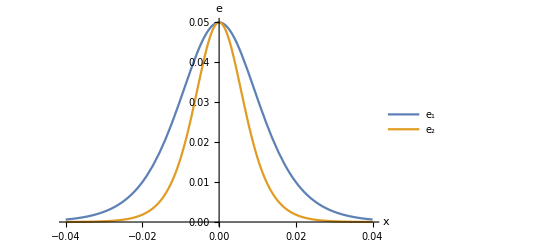

```mathematica
Amp=-0.05;
fig=Plot[{-u1[Amp], -u12[Amp]}, {x, -0.04, 0.04}, AxesLabel->{x,e}, PlotLegends->{"e_1","e_2"}(*TicksStyle->Medium*)]
```

```mathematica
Manipulate[Plot[{u1[A], u12[A]}, {x, -0.04, 0.04}, AxesLabel->{x,e},PlotRange->{0,.5}, PlotLegends->{"e_1","e_2"}],{A,0.1,0.5}]
```

```mathematica
(* Upper velocity limit *)
α11=(1+ν)/4;α21=(-1-ν-ν^2)/2;α31=α11;
α12=(5-5ν-6 ν^2+4 ν^3)/(8(1-ν));α22=-(7-7ν-2 ν^2)/(8(1-ν));α32=1/4;
c=Sqrt[Ε/ρ];
v[a_,b_,d_]=Sqrt[(-b +√(b^2-4 a d))/(2 a)c^2];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
v[α11,α21,α31]^2/c^2-1
v[α12,α22,α32]^2/c^2-1
```

0.510509

0.184995

```mathematica
(3 (-c^2+v[α11,α21,α31]^2) ρ)/β//FullSimplify
(3 (-c^2+v[α12,α22,α32]^2) ρ)/β//FullSimplify
```

-0.204994

-0.0742847

### 2nd Method: multiscale expansion

```mathematica
USeries[x_,r_,t_]=U0[x,r,t]+U1[x,r,t]δ+U2[x,r,t] δ^2+U4[x,r,t] δ^4;
VSeries[x_,r_,t_]=V1[x,r,t]+V2[x,r,t]δ+V3[x,r,t] δ^2+V5[x,r,t] δ^4;
```

```mathematica
V1[x_,r_,t_]=(μ(3λ+2μ)S[x,t]-λ(λ+μ)D[U0[x,t], x])/(2(λ+μ)^2)r+ε FV1[x,r,t];
(*FV1[x_,r_,t_]=CFV1[x,t]r;*)
(*CFV1[x_,t_]=1/(8 (λ+μ)^5)(-μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2+2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t]∂_x U0[x,t]-(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (∂_x U0[x,t])^2);*)
```

```mathematica
ClearAll[CFV1, FV1, V1];
```

```mathematica
ClearAll[U2];
```

```mathematica
U2[x_,r_,t_]=r^2/4(1/μ s^2 ρ D[U0[x,t], t,t]-2 D[U0[x,t], x,x]-(3 λ+2 μ)/(λ+μ)D[S[x,t], x])+ε FU2[x,r,t];
(*FU2[x_,r_,t_]=1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+n r^2 λ^2 S^(1,0)[x,t] U0^(1,0)[x,t]-8 m r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+4 n r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+2 r^2 λ^2 μ S^(1,0)[x,t] U0^(1,0)[x,t]-4 m r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+2 n r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+6 r^2 λ μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+4 r^2 μ^3 S^(1,0)[x,t] U0^(1,0)[x,t]-3 n r^2 λ^2 μ U0^(1,0)[x,t] U0^(2,0)[x,t]-12 m r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-2 n r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-12 r^2 λ^2 μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 m r^2 μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-20 r^2 λ μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 r^2 μ^4 U0^(1,0)[x,t] U0^(2,0)[x,t]+r^2 S[x,t] (-(4 m-n) s^2 (λ+μ) ρ U0^(0,2)[x,t]+(4 m-n) (λ+2 μ) S^(1,0)[x,t]+μ (n λ-2 (λ^2-2 m μ+λ μ)) U0^(2,0)[x,t]));*)
```

```mathematica
n r^2 λ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-8 m r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 n r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 r^2 λ^2 μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-4 m r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 n r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+6 r^2 λ μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 r^2 μ^3 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]//Simplify
```

r^2 (n (λ^2+4 λ μ+2 μ^2)+2 μ (λ^2+3 λ μ+2 μ^2-2 m (2 λ+μ))) S^(1,0)[x,t] U0^(1,0)[x,t]

```mathematica
c1[x_,t_]=1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ Derivative[0,2][S][x,t]-3 s^2 μ ρ Derivative[0,2][S][x,t]+3 s^2 λ^2 ρ Derivative[1,2][U0][x,t]+7 s^2 λ μ ρ Derivative[1,2][U0][x,t]+3 s^2 μ^2 ρ Derivative[1,2][U0][x,t]-λ^2 Derivative[2,0][S][x,t]-2 λ μ Derivative[2,0][S][x,t]-4 λ^2 μ Derivative[3,0][U0][x,t]-11 λ μ^2 Derivative[3,0][U0][x,t]-6 μ^3 Derivative[3,0][U0][x,t]);
V3[x_,r_,t_]=1/(16 μ (λ^2+3 λ μ+2 μ^2))(s^2 μ ρ Derivative[0,2][S][x,t]-s^2 λ^2 ρ Derivative[1,2][U0][x,t]-3 s^2 λ μ ρ Derivative[1,2][U0][x,t]-s^2 μ^2 ρ Derivative[1,2][U0][x,t]+λ^2 Derivative[2,0][S][x,t]+2 λ μ Derivative[2,0][S][x,t]+2 λ^2 μ Derivative[3,0][U0][x,t]+5 λ μ^2 Derivative[3,0][U0][x,t]+2 μ^3 Derivative[3,0][U0][x,t])r^3+c1[x,t]r+ε FV3[x,r,t];
```

```mathematica
U4[x_,r_,t_]=1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (2 r^2 (λ+r^2 λ+r^2 μ) Derivative[3,0][S][x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))+ε FU4[x,r,t];
```

```mathematica
ClearAll[V1,U2,V3,U4,c1];
```

```mathematica
1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+μ (λ+2 μ) (r^2 ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

```mathematica
FU2[x,r,t]/.ForPrint/.ForPrint2
```

1/(16 μ^2 (λ+μ)^2)(n r^2 λ^2 S_x U_0_x-8 m r^2 λ μ S_x U_0_x+4 n r^2 λ μ S_x U_0_x+2 r^2 λ^2 μ S_x U_0_x-4 m r^2 μ^2 S_x U_0_x+2 n r^2 μ^2 S_x U_0_x+6 r^2 λ μ^2 S_x U_0_x+4 r^2 μ^3 S_x U_0_x-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U_0_x U_0_tt-3 n r^2 λ^2 μ U_0_x U_0_xx-12 m r^2 λ μ^2 U_0_x U_0_xx-2 n r^2 λ μ^2 U_0_x U_0_xx-12 r^2 λ^2 μ^2 U_0_x U_0_xx-8 m r^2 μ^3 U_0_x U_0_xx-20 r^2 λ μ^3 U_0_x U_0_xx-8 r^2 μ^4 U_0_x U_0_xx+r^2 S[x,t] ((4 m-n) (λ+2 μ) S_x+(-4 m+n) s^2 (λ+μ) ρ U_0_tt+μ (n λ-2 (λ^2-2 m μ+λ μ)) U_0_xx))

```mathematica
V3[x,r,t]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

ε FV3[x,r,t]+1/(16 μ (λ+μ)^2 (λ+2 μ))r (s^2 μ ((-2+r^2) λ+(-3+r^2) μ) ρ S_(t,t)+λ (λ+2 μ) (-μ+r^2 (λ+μ)) S_(x,x)-s^2 (r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)) ρ U_(0,x,t,t)+μ (λ+2 μ) (r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ)) U_(0,x,x,x))

```mathematica
r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)-(λ+2μ)(r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ))//Simplify
```

-(λ+μ) (r^2 (λ+μ)^2-μ (λ+3 μ))

#### Equations

```mathematica
ClearAll[U4]
```

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧) L/ε/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
cl1=CoefficientList[ndEq1,{ε,δ},{2,4}]//Simplify;
cl2=CoefficientList[ndEq2,{ε,δ},{2,4}]//Simplify;
```

```mathematica
ndEq1red=cl1⟦1+0,1+0⟧+cl1⟦1+1,1+0⟧ε+cl1⟦1+0,1+1⟧δ+cl1⟦1+0,1+2⟧δ^2;
CoefficientList[ndEq1red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{-(μ U_(0,r)+(λ+μ) V_(1,x)+r (μ U_(0,r,r)-s^2 ρ U_(0,t,t)+λ U_(0,x,x)+2 μ U_(0,x,x)+λ V_(1,x,r)+μ V_(1,x,r)))/r,-(μ U_(1,r)+(λ+μ) V_(2,x)+r (μ U_(1,r,r)-s^2 ρ U_(1,t,t)+λ U_(1,x,x)+2 μ U_(1,x,x)+λ V_(2,x,r)+μ V_(2,x,r)))/r,-(μ U_(2,r)+(λ+μ) V_(3,x)+r (μ U_(2,r,r)-s^2 ρ U_(2,t,t)+λ U_(2,x,x)+2 μ U_(2,x,x)+λ V_(3,x,r)+μ V_(3,x,r)))/r,0},{-1/(2 r^2)(V_1 (2 (2 l+λ) V_(1,x)+r ((2 m-n+2 λ) U_(0,r,r)+2 (2 l+λ) U_(0,x,x)+(4 l-2 m+n) V_(1,x,r)))+r U_(0,r) (2 (m+λ+2 μ) U_(0,x)+(4 m-n+4 (λ+μ)) V_(1,r)+2 r (2 (m+λ+2 μ) U_(0,x,r)+(m+λ+2 μ) V_(1,r,r)+(m+μ) V_(1,x,x)))+r (V_(1,r) ((4 l+n+2 μ) V_(1,x)+2 r ((m+λ+2 μ) U_(0,r,r)+(2 l+λ) U_(0,x,x)+(2 l+m+λ+μ) V_(1,x,r)))+2 U_(0,x) ((2 l+m+λ+μ) V_(1,x)+r ((m+λ+2 μ) U_(0,r,r)+(2 l+4 m+3 λ+6 μ) U_(0,x,x)+(2 l+m+λ+μ) V_(1,x,r)))+2 r V_(1,x) (2 (m+μ) U_(0,x,r)+(m+μ) V_(1,r,r)+(m+λ+2 μ) V_(1,x,x)))),0,0,0}}

```mathematica
cl1⟦1+1,1+0⟧/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

-1/(2 r^2)(4 l V_1 V_(1,x)+2 λ V_1 V_(1,x)+4 l r V_(1,r) V_(1,x)+n r V_(1,r) V_(1,x)+2 r μ V_(1,r) V_(1,x)+4 l r V_1 U_(0,x,x)+2 r λ V_1 U_(0,x,x)+4 l r^2 V_(1,r) U_(0,x,x)+2 r^2 λ V_(1,r) U_(0,x,x)+2 m r V_1 U_(2,r,r)-n r V_1 U_(2,r,r)+2 r λ V_1 U_(2,r,r)+2 m r^2 V_(1,r) U_(2,r,r)+2 r^2 λ V_(1,r) U_(2,r,r)+4 r^2 μ V_(1,r) U_(2,r,r)+2 m r^2 V_(1,x) V_(1,r,r)+2 r^2 μ V_(1,x) V_(1,r,r)+r U_(2,r) ((4 m-n+4 (λ+μ)) V_(1,r)+2 r (m+λ+2 μ) V_(1,r,r))+r ((4 l-2 m+n) V_1+2 r (2 l+m+λ+μ) V_(1,r)) V_(1,x,r)+2 r U_(0,x) ((m+λ+2 μ) U_(2,r)+(2 l+m+λ+μ) V_(1,x)+r ((2 l+4 m+3 λ+6 μ) U_(0,x,x)+(m+λ+2 μ) U_(2,r,r)+(2 l+m+λ+μ) V_(1,x,r))))

```mathematica
ndEq2red=cl2⟦1+0,1+0⟧+cl2⟦1+1,1+0⟧ε+cl2⟦1+0,1+1⟧δ+cl2⟦1+0,1+2⟧δ^2;
CoefficientList[ndEq2red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{((λ+2 μ) V_1-r ((λ+2 μ) V_(1,r)+r ((λ+μ) U_(0,x,r)+(λ+2 μ) V_(1,r,r)-s^2 ρ V_(1,t,t)+μ V_(1,x,x))))/r^2,((λ+2 μ) V_2-r ((λ+2 μ) V_(2,r)+r ((λ+μ) U_(1,x,r)+(λ+2 μ) V_(2,r,r)-s^2 ρ V_(2,t,t)+μ V_(2,x,x))))/r^2,((λ+2 μ) V_3-r ((λ+2 μ) V_(3,r)+r ((λ+μ) U_(2,x,r)+(λ+2 μ) V_(3,r,r)-s^2 ρ V_(3,t,t)+μ V_(3,x,x))))/r^2,0},{-1/(4 r^3)(-4 (2 l+2 m+2 λ+3 μ) V_1^2+2 r V_1 (-2 (2 l+λ) U_(0,x)+(4 l-2 m+n) r U_(0,x,r)+2 r (2 l+λ) V_(1,r,r)+r (2 m-n+2 λ) V_(1,x,x))+r^2 ((n+4 μ) U_(0,r)^2+4 (2 l+2 m+2 λ+3 μ) V_(1,r)^2+4 m V_(1,x)^2-n V_(1,x)^2+4 λ V_(1,x)^2+4 μ V_(1,x)^2+4 m r V_(1,x) U_(0,r,r)+4 r μ V_(1,x) U_(0,r,r)+8 l r U_(0,x) U_(0,x,r)+4 m r U_(0,x) U_(0,x,r)+4 r λ U_(0,x) U_(0,x,r)+4 r μ U_(0,x) U_(0,x,r)+4 m r V_(1,x) U_(0,x,x)+4 r λ V_(1,x) U_(0,x,x)+8 r μ V_(1,x) U_(0,x,x)+8 l r U_(0,x) V_(1,r,r)+4 r λ U_(0,x) V_(1,r,r)+8 m r V_(1,x) V_(1,x,r)+8 r λ V_(1,x) V_(1,x,r)+16 r μ V_(1,x) V_(1,x,r)+4 U_(0,r) (r (m+λ+2 μ) U_(0,r,r)+(m+μ) (V_(1,x)+r (U_(0,x,x)+2 V_(1,x,r))))+4 m r U_(0,x) V_(1,x,x)+4 r λ U_(0,x) V_(1,x,x)+8 r μ U_(0,x) V_(1,x,x)+4 V_(1,r) ((2 l+λ) U_(0,x)+r (2 l+m+λ+μ) U_(0,x,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)+r (m+λ+2 μ) V_(1,x,x)))),0,0,0}}

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t]]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+λ) (V_1-r (V_(1,r)+r V_(1,r,r))))/r^2

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t],0]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+2 m+2 λ+3 μ) V_1^2-r^2 (2 l+λ) V_1 V_(1,r,r)-r^2 V_(1,r) ((2 l+2 m+2 λ+3 μ) V_(1,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)))/r^3

```mathematica
Solve[-128 r^2 μ^2 (λ^2+3 λ μ+2 μ^2) c2[x,t]-32 μ^2 (λ^2+3 λ μ+2 μ^2) c3[x,t]+2 r^2 s^4 λ^2 ρ^2 Derivative[0,4][U0][x,t]+6 r^2 s^4 λ μ ρ^2 Derivative[0,4][U0][x,t]+4 r^2 s^4 μ^2 ρ^2 Derivative[0,4][U0][x,t]-2 r^2 s^2 λ^2 ρ Derivative[1,2][S][x,t]+2 s^2 λ μ ρ Derivative[1,2][S][x,t]-8 r^2 s^2 λ μ ρ Derivative[1,2][S][x,t]+3 s^2 μ^2 ρ Derivative[1,2][S][x,t]-6 r^2 s^2 μ^2 ρ Derivative[1,2][S][x,t]-3 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-6 r^2 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-7 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-20 r^2 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-3 s^2 μ^3 ρ Derivative[2,2][U0][x,t]-14 r^2 s^2 μ^3 ρ Derivative[2,2][U0][x,t]+λ^2 μ Derivative[3,0][S][x,t]+4 r^2 λ^2 μ Derivative[3,0][S][x,t]+2 λ μ^2 Derivative[3,0][S][x,t]+12 r^2 λ μ^2 Derivative[3,0][S][x,t]+8 r^2 μ^3 Derivative[3,0][S][x,t]+4 λ^2 μ^2 Derivative[4,0][U0][x,t]+6 r^2 λ^2 μ^2 Derivative[4,0][U0][x,t]+11 λ μ^3 Derivative[4,0][U0][x,t]+18 r^2 λ μ^3 Derivative[4,0][U0][x,t]+6 μ^4 Derivative[4,0][U0][x,t]+12 r^2 μ^4 Derivative[4,0][U0][x,t]==0,c1]
```

{{c1→1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ S^(0,2)[x,t]-3 s^2 μ ρ S^(0,2)[x,t]+3 s^2 λ^2 ρ U0^(1,2)[x,t]+7 s^2 λ μ ρ U0^(1,2)[x,t]+3 s^2 μ^2 ρ U0^(1,2)[x,t]-λ^2 S^(2,0)[x,t]-2 λ μ S^(2,0)[x,t]-4 λ^2 μ U0^(3,0)[x,t]-11 λ μ^2 U0^(3,0)[x,t]-6 μ^3 U0^(3,0)[x,t])}}

```mathematica
DSolve[2 r^3 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+r s^2 (μ (2 λ+3 μ)-2 r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r s^2 ((3+6 r^2) λ^2+(7+20 r^2) λ μ+(3+14 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (r (λ+4 r^2 λ+4 r^2 μ) Derivative[3,0][S][x,t]+r μ (4 λ+6 r^2 λ+3 μ+6 r^2 μ) Derivative[4,0][U0][x,t]-8 μ (λ+μ) (f'[r]+r f''[r])))==0,f,r]
```

{{f→Function[{r},C[2]+1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 U0^(0,4)[x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ S^(1,2)[x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ U0^(2,2)[x,t]+(λ+2 μ) (64 μ (λ+μ) C[1] Log[r]+2 r^2 (λ+r^2 λ+r^2 μ) S^(3,0)[x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) U0^(4,0)[x,t])))]}}

```mathematica
DSolve[-1/(4 r μ (λ+μ)^2)(r s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ Derivative[0,2][U0][x,t] Derivative[1,0][U0][x,t]+μ (r (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t]+4 μ (λ+μ)^2 (f'[r]+r f''[r])))==0,f,r]//Simplify
```

{{f→Function[{r},C[2]+1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+μ (16 μ (λ+μ)^2 C[1] Log[r]-r^2 (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) U0^(1,0)[x,t] U0^(2,0)[x,t]))]}}

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V]
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
cl=CoefficientList[(ndP⟦2,2⟧/.r->1)/ε-μ(3λ+2μ)/(λ+μ)S[x,t],{ε,δ},{2,4}];
cl⟦1+1,1+2⟧=smth;
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,0,λ V_3+λ U_(2,x)+(λ+2 μ) V_(3,1),0},{1/4 (4 λ FV1[x,1,t]+(μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2)/(λ+μ)^4+4 (λ+2 μ) FV1_1-(2 μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U_(0,x))/(λ+μ)^3+((3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x)^2)/(λ+μ)^2),0,smth,0}}

```mathematica
ClearAll[s,λ,μ]
```

```mathematica
(* here would be the equation *)
cl=CoefficientList[((ndP⟦1,2⟧/.r->1)/ε/δ-μ(3λ+2μ)/(λ+μ)T[x,t])2,{ε,δ},{2,4}];
cl⟦1+1,1+2⟧=smth;
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{(-λ μ (3 λ+2 μ) S_x+(λ+μ) (s^2 (λ+μ) ρ U_(0,t,t)-μ (3 λ+2 μ) (U_(0,x,x)+2 T[x,t])))/(λ+μ)^2,0,2 μ (U_(4,1)+V_(3,x)),0},{2 μ FU2_1+m U_(0,x) (-((3 λ+2 μ) S_x)/(λ+μ)+(s^2 ρ U_(0,t,t))/μ-2 U_(0,x,x))+(λ+2 μ) U_(0,x) (-((3 λ+2 μ) S_x)/(λ+μ)+(s^2 ρ U_(0,t,t))/μ-2 U_(0,x,x))+(m (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (-((3 λ+2 μ) S_x)/(λ+μ)+(s^2 ρ U_(0,t,t))/μ-2 U_(0,x,x)))/(λ+μ)^2-(n (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (-((3 λ+2 μ) S_x)/(λ+μ)+(s^2 ρ U_(0,t,t))/μ-2 U_(0,x,x)))/(4 (λ+μ)^2)+((λ+2 μ) (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (-((3 λ+2 μ) S_x)/(λ+μ)+(s^2 ρ U_(0,t,t))/μ-2 U_(0,x,x)))/(λ+μ)^2+(m U_(0,x) (μ (3 λ+2 μ) S_x-λ (λ+μ) U_(0,x,x)))/(λ+μ)^2+(μ U_(0,x) (μ (3 λ+2 μ) S_x-λ (λ+μ) U_(0,x,x)))/(λ+μ)^2+(m (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (μ (3 λ+2 μ) S_x-λ (λ+μ) U_(0,x,x)))/(λ+μ)^4-(n (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (μ (3 λ+2 μ) S_x-λ (λ+μ) U_(0,x,x)))/(4 (λ+μ)^4)+(μ (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_(0,x)) (μ (3 λ+2 μ) S_x-λ (λ+μ) U_(0,x,x)))/(2 (λ+μ)^4)+1/(4 (λ+μ)^5)μ (-2 μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t] S_x+2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x U_(0,x)+2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U_(0,x,x)-2 (λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x) U_(0,x,x))-((-μ (3 λ+2 μ) S[x,t]+λ (λ+μ) U_(0,x)) (μ (3 λ+2 μ) S_x+(λ+μ) (-s^2 ρ U_(0,t,t)+2 μ U_(0,x,x))))/(λ+μ)^3,0,smth,0}}

```mathematica
Solve[(16 (λ+μ)^2 (λ+2 μ) c1[x,t]-s^2 (3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][U0][x,t]+μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][U0][x,t])/(8 (λ+μ) (λ+2 μ))==0,c1[x,t]]//Simplify
```

{{c1[x,t]→(s^2 (3 λ^2+7 λ μ+3 μ^2) ρ U0^(1,2)[x,t]-μ (4 λ^2+11 λ μ+6 μ^2) U0^(3,0)[x,t])/(16 (λ+μ)^2 (λ+2 μ))}}

#### Final equation

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
s=Sqrt[Ε/ρ];
```

```mathematica
cl=CoefficientList[(2ndP⟦2,1⟧/.r->1)/ε/δ/Ε,{ε,δ},{2,4}];
Series[cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε+O[ε]^2)+1/4 ((1+ν) U_0_tttt-2 (1+ν+ν^2) U_0_xxtt+(1+ν) U_0_xxxx) δ^2+O[δ]^3

### 3rd Method: variational method (Lagrangian)

```mathematica
ClearAll[U,V];
Lagr=r(ρ Total[(D[Displace, t])^2]/2-Pot);
VarSubst={
Derivative[i__][U][x__]-> (Derivative[i][U][x]+δ Derivative[i][δU][x]),
Derivative[i__][V][x__]-> (Derivative[i][V][x]+δ Derivative[i][δV][x]),
U[x__]->U[x]+δ δU[x],V[x__]->V[x]+δ δV[x]};
δLagr=Coefficient[(Lagr/.VarSubst)-Lagr,δ]//Simplify;
δLagr/.ForPrint/.ForPrint2
```

-1/(4 r^5)(-4 r^6 ρ (U_t δU_t+V_t δV_t)+2 r^2 (λ+2 μ) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(l+2 m) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2))^2 (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+n r^4 (-V (2 r+V) (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)+V (2 r+V) ((2 U_x+U_x^2+V_x^2) (U_r δU_r+(1+V_r) δV_r)+(U_r^2+V_r (2+V_r)) ((1+U_x) δU_x+V_x δV_x))-(r+V) (U_r (1+U_x)+(1+V_r) V_x)^2 δV[x,r,t]+(r+V) (U_r^2+V_r (2+V_r)) (2 U_x+U_x^2+V_x^2) δV[x,r,t])-4 r^4 μ (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))-2 m r^2 ((-2 r^2 U_r (1+U_x) (1+V_r) V_x+r^2 (2 U_x (2+U_x) V_r+U_x (2+U_x) V_r^2-V_x^2)+2 r V (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+V^2 (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+U_r^2 (2 r V+V^2+r^2 (-1+V_x^2))) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))))

```mathematica
CUt=Coefficient[δLagr,D[δU[x,r,t], t]];
CVt=Coefficient[δLagr,D[δV[x,r,t], t]];
CU=Coefficient[δLagr,δU[x,r,t]]//Simplify;
CV=Coefficient[δLagr,δV[x,r,t]]//Simplify;
CUx=Coefficient[δLagr,D[δU[x,r,t], x]]//Simplify;
CVr=Coefficient[δLagr,D[δV[x,r,t], r]]//Simplify;
CUr=Coefficient[δLagr,D[δU[x,r,t], r]]//Simplify;
CVx=Coefficient[δLagr,D[δV[x,r,t], x]]//Simplify;
```

#### Equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2(*δ^2*)+U4[x,t] r^4(*δ^4*);
VSeries[x_,r_,t_]=V1[x,t]r (*δ*)(*+V2[x,t] r^2 δ^2*)+V3[x,t] r^3(*δ^3*);
```

```mathematica
ClearAll[U,V]
Eq1=D[CUt, t]-CU+D[CUx, x]+D[CUr, r];
Eq2=D[CVt, t]-CV+D[CVx, x]+D[CVr, r];
ndEq1=(Eq1/.Scales2)/ε/r;
ndEq2=(Eq2/.Scales2)/ε/r/r;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
cl1=CoefficientList[ndEq1,{ε,r},{2,3}];
cl2=CoefficientList[ndEq2,{ε,r},{2,3}];
ndEq1Red=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧r^2;
ndEq2Red=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧r^2;
ndEq1Int=Integrate[ndEq1Red/δ,{r,0,δ}];
ndEq2Int=Integrate[ndEq2Red/δ,{r,0,δ}];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
```

```mathematica
cl1//Simplify
cl2//Simplify
```

{{-4 μ U2[x,t]+s^2 ρ U0^(0,2)[x,t]-2 λ V1^(1,0)[x,t]-2 μ V1^(1,0)[x,t]-λ U0^(2,0)[x,t]-2 μ U0^(2,0)[x,t],0,-16 μ U4[x,t]+s^2 ρ U2^(0,2)[x,t]-4 λ V3^(1,0)[x,t]-4 μ V3^(1,0)[x,t]-λ U2^(2,0)[x,t]-2 μ U2^(2,0)[x,t]},{-2 U2[x,t] ((4 m-n+4 (λ+μ)) V1[x,t]+2 (m+λ+2 μ) U0^(1,0)[x,t])-V1[x,t] ((8 l+n+2 (λ+μ)) V1^(1,0)[x,t]+2 (2 l+λ) U0^(2,0)[x,t])-U0^(1,0)[x,t] (2 (2 l+m+λ+μ) V1^(1,0)[x,t]+(2 l+4 m+3 λ+6 μ) U0^(2,0)[x,t]),0,0}}

{{-8 (λ+2 μ) V3[x,t]+s^2 ρ V1^(0,2)[x,t]-2 λ U2^(1,0)[x,t]-2 μ U2^(1,0)[x,t]-μ V1^(2,0)[x,t],0,s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]},{-(4 m+n+4 (λ+3 μ)) U2[x,t]^2-16 l V3[x,t] U0^(1,0)[x,t]-8 λ V3[x,t] U0^(1,0)[x,t]-4 l U0^(1,0)[x,t] U2^(1,0)[x,t]-2 m U0^(1,0)[x,t] U2^(1,0)[x,t]-2 λ U0^(1,0)[x,t] U2^(1,0)[x,t]-2 μ U0^(1,0)[x,t] U2^(1,0)[x,t]-3 m (V1^(1,0)[x,t])^2+1/4 n (V1^(1,0)[x,t])^2-3 λ (V1^(1,0)[x,t])^2-5 μ (V1^(1,0)[x,t])^2-m V1^(1,0)[x,t] U0^(2,0)[x,t]-λ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 μ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 (m+μ) U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])-m U0^(1,0)[x,t] V1^(2,0)[x,t]-λ U0^(1,0)[x,t] V1^(2,0)[x,t]-2 μ U0^(1,0)[x,t] V1^(2,0)[x,t]-1/2 V1[x,t] (32 (2 l+2 m+2 λ+3 μ) V3[x,t]+2 (8 l+n+2 (λ+μ)) U2^(1,0)[x,t]+(4 m-n+4 (λ+μ)) V1^(2,0)[x,t]),0,0}}

```mathematica
ClearAll[V1,U2,V3,U4,FV3,FU2]
```

```mathematica
U4[x_,t_]=Solve[cl1⟦1,3⟧==0,U4[x,t]]⟦1,1,2⟧;
```

```mathematica
V3[x_,t_]=Solve[cl2⟦1,1⟧==0,V3[x,t]]⟦1,1,2⟧+ε FV3[x,t];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
FV3[x_,t_]=Solve[cl2⟦2,1⟧==0,FV3[x,t]]⟦1,1,2⟧;
```

```mathematica
U2[x_,t_]=Solve[cl1⟦1,1⟧==0,U2[x,t]]⟦1,1,2⟧+ε FU2[x,t];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
FU2[x_,t_]=Solve[cl1⟦2,1⟧==0,FU2[x,t]]⟦1,1,2⟧;
```

The terms above coincides with those derived by the 1st method

```mathematica
U2[x_,t_]=U2[x,t]//Simplify;
V3[x_,t_]=V3[x,t]//Simplify;
```

#### Boundary conditions

```mathematica
ClearAll[U,V,V1,f]
```

```mathematica
bound={r->δ};
```

```mathematica
ClearAll[U,V,V1,f]
bound={r->δ};
ndBC1=((-CUr/.Scales2/.bound)/ε/L/δ/δ-μ(3λ+2μ)/(λ+μ) T[x,t])//Simplify;
ndBC2=((-CVr/.Scales2/.bound)/ε/L/δ-μ(3λ+2μ)/(λ+μ) S[x,t])//Simplify;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
ndBC1Red=Coefficient[ndBC1,ε,0]+Coefficient[ndBC1,ε,1]ε;
ndBC2Red=Coefficient[ndBC2,ε,0]+Coefficient[ndBC2,ε,1]ε;
cl1=CoefficientList[2ndBC1Red,{ε,δ},{2,3}];
cl2=CoefficientList[ndBC2Red,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
ndBC2RedRed=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧δ^2;
```

```mathematica
ClearAll[V1,f,g]
```

```mathematica
V1[x_,t_]=((Solve[cl2⟦1,1⟧==0,V1[x,t]]⟦1,1,2⟧//Simplify)
+f[x,t] δ^2+g[x,t]ε);
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
f[x_,t_]=Solve[cl2⟦1,3⟧==0,f[x,t]]⟦1,1,2⟧//Simplify;
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
g[x_,t_]=Solve[cl2⟦2,1⟧==0,g[x,t]]⟦1,1,2⟧//Simplify;
V1[x,t]/.ForPrint/.ForPrint2
```

(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_0_x)/(2 (λ+μ)^2)-1/(8 (λ+μ)^5)ε (μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2-2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U_0_x+(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (U_0)_x^2)-1/(16 (λ+μ)^3 (λ+2 μ))δ^2 (s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S_tt-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U_0_xtt+μ (λ+2 μ) (λ (3 λ+2 μ) S_xx+(4 λ^2+7 λ μ+3 μ^2) U_0_xxx))

```mathematica
cl1=CoefficientList[-ndBC1RedRed,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
cl1=CoefficientList[ndBC1RedRed,{ε,δ},{2,3}]//Simplify
```

{{1/(λ+μ)^2(2 μ (3 λ^2+5 λ μ+2 μ^2) T[x,t]-s^2 (λ+μ)^2 ρ U0^(0,2)[x,t]+μ (3 λ+2 μ) (λ S^(1,0)[x,t]+(λ+μ) U0^(2,0)[x,t])),0,1/8 (-(s^4 ρ^2 U0^(0,4)[x,t])/μ+1/(λ+μ)^3(s^2 (3 λ^3+5 λ^2 μ+5 λ μ^2+2 μ^3) ρ S^(1,2)[x,t]+s^2 (7 λ^3+17 λ^2 μ+14 λ μ^2+4 μ^3) ρ U0^(2,2)[x,t]-μ (3 λ+2 μ) ((4 λ^2+5 λ μ+2 μ^2) S^(3,0)[x,t]+(3 λ^2+5 λ μ+2 μ^2) U0^(4,0)[x,t])))},{1/(2 (λ+μ)^5)(μ (3 λ+2 μ) S[x,t] (-μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S^(1,0)[x,t]+(λ+μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U0^(2,0)[x,t])+(λ+μ) U0^(1,0)[x,t] (μ (3 λ+2 μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S^(1,0)[x,t]+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U0^(2,0)[x,t])),0,0}}

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/(1+ν)/2;
cl1=cl1/Ε//FullSimplify;
```

```mathematica
cl1/.ForPrint
```

{{2 ν S_x-U0_tt+U0_xx+2 T[x,t],0,1/4 ((1+ν) (1-2 ν+4 ν^2) S_xtt-S_xxx-(1+ν) U0_tttt+2 U0_xxtt+ν (-(1+2 ν) S_xxx+2 (1+ν) U0_xxtt-U0_xxxx)-U0_xxxx)},{1/Ε(U0_x (-2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m+3 Ε-2 l (-1+2 ν)^3-2 ν^2 (-3 n+m (6+4 ν))) U0_xx)-2 (1+ν) S[x,t] ((-1+2 ν) (n+2 m (1+ν) (-1+2 ν) (1+2 ν)-ν (n+2 Ε+2 n ν)+4 l (1-3 ν+4 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U0_xx)),0,0}}

```mathematica
(* Dispersive coefficients *)
c1=Coefficient[cl1⟦1,3⟧, Derivative[0,4][U0][x,t]]
c2=Coefficient[cl1⟦1,3⟧, Derivative[2,2][U0][x,t]]//Simplify
c3=Coefficient[cl1⟦1,3⟧, Derivative[4,0][U0][x,t]]//Simplify
c1+c2+c3//Simplify
```

1/4 (-1-ν)

1/2 (1+ν+ν^2)

1/4 (-1-ν)

ν^2/2

```mathematica
(* Nonlinear coefficients *)
b1=Coefficient[cl1⟦2,1⟧, Derivative[1,0][U0][x,t]Derivative[2,0][U0][x,t]]//FullSimplify
```

(3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3)/Ε

### Plot

#### PS constants

```mathematica
ρ=1060;
Ε=3.7*10^9;
ν=0.34;
l =-1.89*10^10;
m= -1.33*10^10;
n=-10^10;
```

#### PMMA constants

```mathematica
ρ=1180;
Ε=4.9*10^9;
ν=0.34;
l =-10.93*10^9;
m= -7.73*10^9;
n=-1.41*10^9;
```

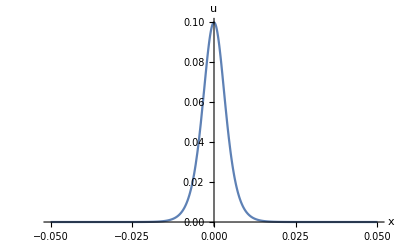

```mathematica
A=-0.1;
R=5*10^-3;
c=Sqrt[Ε/ρ];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
d=β/(2ρ);
a=-((ν+1)R^2)/4;
b=(ν^2+ν+1)R^2/2;
u[x_,t_]=A Sech[(√(3/2) √(A d)c)/(√(b (9 c^4+6 A c^2 d)+2 a (9 c^4+6 A c^2 d+2 A^2 d^2)))(x-Sqrt[c^2+2/3 A d] t)]^2;
(*u0[x_,l_,m_,n_]=A Sech[Sqrt[(A d)/(6(a c^2+b+2/3 A d a))](x)]^2;*)
Plot[-u[x,0],{x,-0.05,0.05},PlotRange->All,AxesLabel->{x,u}]
```

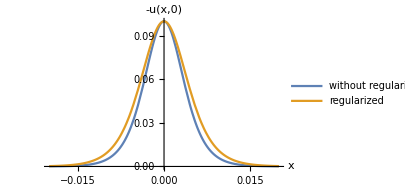

```mathematica
b=ν^2 R^2/2;
uReg[x_,t_]=A Sech[Sqrt[(A d)/(2b (3 c^2+2 A d))](x-Sqrt[c^2+2/3 A d] t)]^2;
fig=Plot[{-u[x,0],-uReg[x,0]},{x,-0.02,0.02},PlotRange->All,PlotLegends->Placed[{"without regularization", "regularized"},Bottom],PlotRange->All,AxesLabel->{x,"-u(x,0)"},ImageSize->300]
```

```mathematica
Export["reg_nonreg_compar.eps",fig]
Directory[]
```

reg_nonreg_compar.eps

/home/feodor

```mathematica
Directory[]
```

/home/theodor

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/theodor/Dropbox/Ioffe/Wolfram Mathematica code

### Dispersive relation

```mathematica
ClearAll[u,eq]
```

```mathematica
eq=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2(ν^2+ν+1)D[u[x,t], x,x,t,t]+1/4(1+ν)δ^2(D[u[x,t], t,t,t,t]+D[u[x,t], x,x,x,x]);
```

```mathematica
eq=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]+R^2(b D[u[x,t], x,x,t,t]+a/c^2 D[u[x,t], t,t,t,t]+d c^2 D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=Exp[I(k/R x - ω c/R t)];
disp=eq/Exp[I(k/R x - ω c/R t)]//Simplify
```

(c^2 (k^2+d k^4-ω^2+b k^2 ω^2+a ω^4))/R^2

```mathematica
Solve[disp==0,ω]//Simplify
```

{{ω→-(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→-(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)}}

```mathematica
Series[(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν)),{δ,0,2}]
```

ω^2-1/2 (ν^2 ω^4) δ^2+O[δ]^3

```mathematica
(2+δ^2 (1+ν+ν^2) ω^2)^2-(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4)//Simplify
```

δ^2 (1+ν) ω^2 (4+δ^2 (1+ν) ω^2)

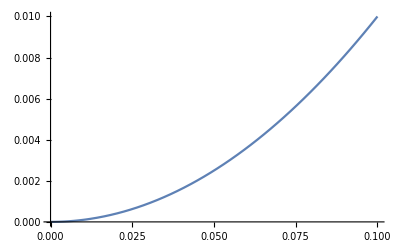

```mathematica
k2=(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν))/.{δ->0.5,ν->1/3};
Plot[k2,{ω,0,0.1}]
```

```mathematica
eqreg=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2 ν^2 D[u[x,t], x,x,t,t];
dispreg=eqreg/ⅇ^(k x-t ω)//Simplify
Solve[dispreg==0,k]//Simplify
```

ω^2-1/2 k^2 (2+δ^2 ν^2 ω^2)

{{k→-ω/(√(1+1/2 δ^2 ν^2 ω^2))},{k→ω/(√(1+1/2 δ^2 ν^2 ω^2))}}

### Plasticity

```mathematica
ndPred={
{ndPxxRed,ndPxrRed,0},
{ndPrxRed,ndPrrRed,0},
{0,0,0}
};
```

```mathematica
For[i=1,i<3,i++,
For[j=1,j<3,j++,
cl=CoefficientList[ndPred⟦i,j⟧,{ε,δ},{2,4}];
ndPred⟦i,j⟧=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
];
];
Clear[i,j];
```

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L,γ->γ/ε};
```

```mathematica
ClearAll[U0,ν,l,m,n,Ε,ρ,R,A]
```

```mathematica
(* Compute only once *)
ndPred⟦1,2⟧=δ ndPred⟦1,2⟧;
ndPred⟦2,1⟧=δ ndPred⟦2,1⟧;
ndPred=ε ndPred;
```

```mathematica
Pred=ndPred/.InvScales//Simplify;
```

```mathematica
VonMises[x_,r_,t_]=-3Inv2[Pred-IdentityMatrix[3]*Tr[Pred]/3]//Simplify;
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));μ=Ε/(2(1+ν));
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
s=Sqrt[(Ε+γ β)/ρ];
B[a_,b_,d_]=Sqrt[(3A β s^2 ρ)/(-4 R^2 (a (A β+3 s^2 ρ)^2+3 s^2 ρ (A b β+3 s^2 (b+d) ρ)))];
v=Sqrt[s^2+(A β)/(3ρ)];
```

```mathematica
u0[x_,t_]=(A-3γ) (Cosh [B[(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4](x-v t)])^-2;
```

```mathematica
U0[x_,t_]=Integrate[u0[x,t],x];
```

```mathematica
R=0.01;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
VonMisesA[A_,γ_,x_,r_,t_]=VonMises[x,r,t];
```

```mathematica
Manipulate[{Sqrt[VonMisesA[A,γ,0,0,0]],A-3γ},{A,-0.1,0.3},{γ,-0.1,0.1}]
```

```mathematica
xarr=Array[#&,11,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,5,{0,R}];
Max[vmarr]
```

2.51452×10^17

Soliton of extension is not elastic in PS rod.
PS yield stress: 86 MPa (extension),  114 MPa (compression).

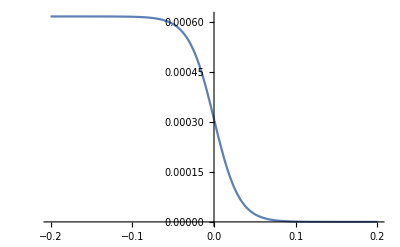

```mathematica
Plot[U0[x,0,0],{x,-.2,.2}]
```

```mathematica
(* Linear stress tensor *)
Displace0={U0[x,r,t],V01[x,r,t],0};
Deform0=RotateRight[Grad[RotateLeft[Displace0,1],{r,ϕ,x},"Cylindrical"],{1,1}];
SGr0=(Transpose[Deform0]+Deform0)/2;
P0=λ Inv1[SGr0]IdentityMatrix[3]+2μ SGr0//Simplify;
```

```mathematica
P0
```

{{-(3.7×10^7)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^2,-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.},{-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.,0.},{0.,0.,0.}}

```mathematica
(* Von Mises stress *)
VonMises[x_,r_,t_]=-3Inv2[P0-IdentityMatrix[3]*Tr[P0]/3]//Simplify
```

-(1.369×10^15)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^4-2.78862×10^17 r^2 Sech[32.4757 (-1891.43 t+x)]^4 Tanh[32.4757 (-1891.43 t+x)]^2

```mathematica
xarr=Array[#&,101,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,11,{0,R}];
Max[vmarr]
```

### Linear equations (following Bostrom)

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
U[x_,r_,t_]=Subscript[U, 0][x,t]+Subscript[U, 2][x,t] r^2+Subscript[U, 4][x,t] r^4;
V[x_,r_,t_]=Subscript[U, 1][x,t]r+Subscript[U, 3][x,t] r^3;
order=2;
Print["Equation 1:"]
Series[ρ D[U[x,r,t], t,t]-divPK⟦1⟧,{r,0,order}]//FullSimplify
Print["Equation 2:"]
Series[ρ D[V[x,r,t], t,t]-divPK⟦2⟧,{r,0,order}]//FullSimplify
```

Equation 1:

O[r]^3

Equation 2:

O[r]^3

```mathematica
Subscript[U, 2][x_,t_]=(ρ Derivative[0,2][Subscript[U, 0]][x,t]-2 (λ+μ) Derivative[1,0][Subscript[U, 1]][x,t]-(λ+2 μ) Derivative[2,0][Subscript[U, 0]][x,t])/(4μ);
```

```mathematica
Subscript[U, 3][x_,t_]=(ρ Derivative[0,2][Subscript[U, 1]][x,t]-2 (λ+μ) Derivative[1,0][Subscript[U, 2]][x,t]-μ Derivative[2,0][Subscript[U, 1]][x,t])/8 /(λ+2 μ);
```

```mathematica
Subscript[U, 4][x_,t_]=(ρ Derivative[0,2][Subscript[U, 2]][x,t]-4 (λ+μ) Derivative[1,0][Subscript[U, 3]][x,t]-(λ+2 μ) Derivative[2,0][Subscript[U, 2]][x,t])/(16μ);
```

```mathematica
order=3;
Print["P_rr = "]
Series[P⟦2,2⟧,{r,0,order}]//Simplify
Print["P_rx = "]
Series[P⟦2,1⟧,{r,0,order}]//Simplify
```

P_rr =

(2 (λ+μ) U_1[x,t]+λ U_0^(1,0)[x,t])+1/(8 (λ+2 μ))((4 λ ρ+6 μ ρ) U_1^(0,2)[x,t]-(λ+3 μ) ρ U_0^(1,2)[x,t]+(λ+2 μ) (2 λ U_1^(2,0)[x,t]+(λ+3 μ) U_0^(3,0)[x,t])) r^2+O[r]^4

P_rx =

1/2 (ρ U_0^(0,2)[x,t]-2 λ U_1^(1,0)[x,t]-(λ+2 μ) U_0^(2,0)[x,t]) r+1/(16 μ (λ+2 μ))((λ+2 μ) ρ^2 U_0^(0,4)[x,t]-2 (λ^2+4 λ μ+2 μ^2) ρ U_1^(1,2)[x,t]-λ^2 ρ U_0^(2,2)[x,t]-7 λ μ ρ U_0^(2,2)[x,t]-8 μ^2 ρ U_0^(2,2)[x,t]+6 λ^2 μ U_1^(3,0)[x,t]+16 λ μ^2 U_1^(3,0)[x,t]+8 μ^3 U_1^(3,0)[x,t]+3 λ^2 μ U_0^(4,0)[x,t]+10 λ μ^2 U_0^(4,0)[x,t]+8 μ^3 U_0^(4,0)[x,t]) r^3+O[r]^4

```mathematica
Prr[x_,t_]=(2 (λ+μ) Subscript[U, 1][x,t]+λ Derivative[1,0][Subscript[U, 0]][x,t])+1/(8 (λ+2 μ))((4 λ ρ+6 μ ρ) Derivative[0,2][Subscript[U, 1]][x,t]-(λ+3 μ) ρ Derivative[1,2][Subscript[U, 0]][x,t]+(λ+2 μ) (2 λ Derivative[2,0][Subscript[U, 1]][x,t]+(λ+3 μ) Derivative[3,0][Subscript[U, 0]][x,t])) r^2/.r->a;
Prx[x_,t_]=1/2 (ρ Derivative[0,2][Subscript[U, 0]][x,t]-2 λ Derivative[1,0][Subscript[U, 1]][x,t]-(λ+2 μ) Derivative[2,0][Subscript[U, 0]][x,t]) r+1/(16 μ (λ+2 μ))((λ+2 μ) ρ^2 Derivative[0,4][Subscript[U, 0]][x,t]-2 (λ^2+4 λ μ+2 μ^2) ρ Derivative[1,2][Subscript[U, 1]][x,t]-λ^2 ρ Derivative[2,2][Subscript[U, 0]][x,t]-7 λ μ ρ Derivative[2,2][Subscript[U, 0]][x,t]-8 μ^2 ρ Derivative[2,2][Subscript[U, 0]][x,t]+6 λ^2 μ Derivative[3,0][Subscript[U, 1]][x,t]+16 λ μ^2 Derivative[3,0][Subscript[U, 1]][x,t]+8 μ^3 Derivative[3,0][Subscript[U, 1]][x,t]+3 λ^2 μ Derivative[4,0][Subscript[U, 0]][x,t]+10 λ μ^2 Derivative[4,0][Subscript[U, 0]][x,t]+8 μ^3 Derivative[4,0][Subscript[U, 0]][x,t]) r^3/.r->a;
```

```mathematica
ν=λ/(2(λ+μ));
Ε=(μ(3λ+2μ))/(λ+μ);
```

```mathematica
γ1=((λ^2+4λ μ+2 μ^2)(3λ+2μ))/(2(λ+μ)^2(λ+2μ));
γ2=Ε/μ;
β=(μ(2λ+3μ)(3λ+2μ))/(2(λ+μ)^2(λ+2μ));
```

```mathematica
Series[(2ν D[Prr[x,t], x]+a^2/8(γ1/(Ε/ρ)D[Prr[x,t], x,t,t]-γ2 D[Prr[x,t], x,x,x]))1/Ε,{a,0,2}]//Simplify
```

(λ (2 (λ+μ) U_1^(1,0)[x,t]+λ U_0^(2,0)[x,t]))/(μ (3 λ+2 μ))+((2 (λ^3+9 λ^2 μ+12 λ μ^2+2 μ^3) ρ U_1^(1,2)[x,t]+λ (λ^2+2 λ μ-4 μ^2) ρ U_0^(2,2)[x,t]-2 μ (λ+2 μ) (2 (2 λ^2+5 λ μ+2 μ^2) U_1^(3,0)[x,t]+λ (2 λ-μ) U_0^(4,0)[x,t])) a^2)/(16 μ^2 (λ+2 μ) (3 λ+2 μ))+O[a]^3

```mathematica
Series[(2Prx[x,t]+a^2/2(β/(Ε/ρ)D[Prx[x,t], t,t]+ν D[Prx[x,t], x,x]))1/(a Ε),{a,0,2}]//Simplify
```

-((λ+μ) (-ρ U_0^(0,2)[x,t]+2 λ U_1^(1,0)[x,t]+(λ+2 μ) U_0^(2,0)[x,t]))/(μ (3 λ+2 μ))+(((λ^2+5 λ μ+5 μ^2) ρ^2 U_0^(0,4)[x,t]-2 (λ^3+7 λ^2 μ+9 λ μ^2+2 μ^3) ρ U_1^(1,2)[x,t]-λ^3 ρ U_0^(2,2)[x,t]-9 λ^2 μ ρ U_0^(2,2)[x,t]-20 λ μ^2 ρ U_0^(2,2)[x,t]-14 μ^3 ρ U_0^(2,2)[x,t]+4 λ^3 μ U_1^(3,0)[x,t]+18 λ^2 μ^2 U_1^(3,0)[x,t]+24 λ μ^3 U_1^(3,0)[x,t]+8 μ^4 U_1^(3,0)[x,t]+2 λ^3 μ U_0^(4,0)[x,t]+9 λ^2 μ^2 U_0^(4,0)[x,t]+14 λ μ^3 U_0^(4,0)[x,t]+8 μ^4 U_0^(4,0)[x,t]) a^2)/(8 μ^2 (λ+2 μ) (3 λ+2 μ))+O[a]^3

```mathematica
Series[(2ν D[Prr[x,t], x]+a^2/8(γ1/(Ε/ρ)D[Prr[x,t], x,t,t]-γ2 D[Prr[x,t], x,x,x]))1/Ε+(2Prx[x,t]+a^2/2(β/(Ε/ρ)D[Prx[x,t], t,t]+ν D[Prx[x,t], x,x]))1/(a Ε),{a,0,2}]//FullSimplify
```

(((λ+μ) ρ U_0^(0,2)[x,t])/(μ (3 λ+2 μ))-U_0^(2,0)[x,t])+1/16 ((ρ (2 (λ^2+5 λ μ+5 μ^2) ρ U_0^(0,4)[x,t]-2 (λ+μ) (λ^2+4 λ μ+2 μ^2) U_1^(1,2)[x,t]-(λ^3+16 λ^2 μ+44 λ μ^2+28 μ^3) U_0^(2,2)[x,t]))/(μ^2 (λ+2 μ) (3 λ+2 μ))+4 U_0^(4,0)[x,t]) a^2+O[a]^3

```mathematica
Subscript[U, 1][x_,t_]=-λ Derivative[1,0][Subscript[U, 0]][x,t]/2/(λ+μ)+r^2((3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][Subscript[U, 0]][x,t]-μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][Subscript[U, 0]][x,t])/(16 (λ+μ)^2 (λ+2 μ));
```

```mathematica
Coefficient[P⟦2,1⟧,Derivative[0,4][Subscript[U, 0]][x,t] r^3]//Simplify
```

ρ^2/(16 μ)

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
c=Sqrt[(μ(3λ+2μ))/(ρ(λ+μ))];
ν=0.34;
((λ^2+5λ μ+5 μ^2)(3λ+2μ))/(2(λ+μ)^2(λ+2μ))//Simplify
```

2.09365

```mathematica
(6 λ^2+21λ μ+14 μ^2)/(2(λ+μ)(λ+2μ))
```

3.32485

```mathematica
(6 λ^2+21λ μ+14 μ^2)/(2(λ+μ)(λ+2μ))-((λ^2+5λ μ+5 μ^2)(3λ+2μ))/(2(λ+μ)^2(λ+2μ))-1//FullSimplify
```

2 ν^2

```mathematica
ε=0;
r=1;
s=1;
```

```mathematica
Series[ndPrrFin,{δ,0,3}]/.ForPrint//Simplify
Series[ndPrxFin,{δ,0,3}]/.ForPrint//Simplify
```

(λ U0_x+2 (λ+μ) V_1)+1/(8 (λ+2 μ))(-s^2 (λ+3 μ) ρ U0_xtt+(λ^2+5 λ μ+6 μ^2) U0_xxx+4 s^2 λ ρ V1_tt+6 s^2 μ ρ V1_tt+2 λ^2 V1_xx+4 λ μ V1_xx) δ^2+O[δ]^4

1/2 (s^2 ρ U0_tt-(λ+2 μ) U0_xx-2 λ V1_x)+1/(16 μ (λ+2 μ))(s^4 (λ+2 μ) ρ^2 U0_tttt-s^2 (λ^2+7 λ μ+8 μ^2) ρ U0_xxtt+3 λ^2 μ U0_xxxx+10 λ μ^2 U0_xxxx+8 μ^3 U0_xxxx-2 s^2 λ^2 ρ V1_xtt-8 s^2 λ μ ρ V1_xtt-4 s^2 μ^2 ρ V1_xtt+6 λ^2 μ V1_xxx+16 λ μ^2 V1_xxx+8 μ^3 V1_xxx) δ^2+O[δ]^4

```mathematica
Series[(ndPrxFin+λ/(2(λ+μ))D[ndPrrFin, x]+δ^2(s^2 ρ(λ^2+λ μ+μ^2))/(16(λ+μ)^2 μ)D[ndPrrFin, x,t,t]-δ^2(4 λ^2+5 λ μ+2 μ^2)/(16 (λ+μ)^2)D[ndPrrFin, x,x,x])(λ+μ)/(μ (3 λ+2 μ)),{δ,0,3}]/.ForPrint//Simplify
```

1/2 (((λ+μ) ρ U0_tt)/(μ (3 λ+2 μ))-U0_xx)+(((λ+μ)^2 ρ^2 U0_tttt+μ (-(7 λ^2+10 λ μ+4 μ^2) ρ U0_xxtt+μ (3 λ+2 μ)^2 U0_xxxx)) δ^2)/(16 μ^2 (λ+μ) (3 λ+2 μ))+O[δ]^4

### Test

```mathematica
Displace={U[x,r,ϕ],V[x,r,ϕ],W[x,r,ϕ]};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
Deform//MatrixForm
```

(U^(1,0,0)[x,r,ϕ] | U^(0,1,0)[x,r,ϕ] | (U^(0,0,1)[x,r,ϕ])/r
V^(1,0,0)[x,r,ϕ] | V^(0,1,0)[x,r,ϕ] | (-W[x,r,ϕ]+V^(0,0,1)[x,r,ϕ])/r
W^(1,0,0)[x,r,ϕ] | W^(0,1,0)[x,r,ϕ] | (V[x,r,ϕ]+W^(0,0,1)[x,r,ϕ])/r)

```mathematica
SGrD=DiagonalMatrix[{l1, l2, l3}];
I1 = Inv1[SGrD];
I2 = Inv2[SGrD];
I3 = Inv3[SGrD];
Pot[l1_,l2_,l3_]=(λ+2 μ)/2 I1^2-2 μ I2+(l+2 m)/3 I1^3-2 m I1 I2+n I3
```

-(l1+l2+l3) (-l1^2-l2^2-l3^2+(l1+l2+l3)^2) m+1/3 (l1+l2+l3)^3 (l+2 m)+l1 l2 l3 n-(-l1^2-l2^2-l3^2+(l1+l2+l3)^2) μ+1/2 (l1+l2+l3)^2 (λ+2 μ)

```mathematica
Pot[ε,γ,ε]//Simplify
```

n γ ε^2+2/3 m (γ-ε)^2 (γ+2 ε)+1/3 l (γ+2 ε)^3+(γ^2 λ)/2+2 γ ε λ+2 ε^2 λ+γ^2 μ+2 ε^2 μ

```mathematica
(1-(D[Pot[ε,γ,ε], γ,ε])^2/(D[Pot[ε,γ,ε], γ,γ]D[Pot[ε,γ,ε], ε,ε]))D[Pot[ε,γ,ε], γ,γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//FullSimplify
```

(γ λ^2 (-(-6 m+n)^2 γ+6 n λ)+4 λ ((3 l n+4 m (-3 m+n)) γ^2+3 (m+n) γ λ+3 λ^2) μ+2 (4 m (-2 m+n) γ^2+5 (2 m+n) γ λ+16 λ^2+2 l γ (6 m γ+n γ+6 λ)) μ^2+4 ((6 l+2 m+n) γ+7 λ) μ^3+8 μ^4)/(2 (λ+μ) (4 l γ μ+n γ (λ+μ)+2 (λ+μ)^2-2 m γ (2 λ+μ)))

```mathematica
γ/(γ^2-ε^2) D[Pot[ε,γ,ε], γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//Simplify
```

(n γ λ^2+4 μ (3 λ^2+l γ μ+5 λ μ+2 μ^2)+2 m γ (3 λ^2+8 λ μ+4 μ^2))/(3 λ^2+8 λ μ+4 μ^2)

## High frequency

```mathematica
Scales={Derivative[i_,j_,k_][U][x_,r_,t_]->(Derivative[i,j,k][U][x,r,t])/(L^(i+j+k)s^-k)ε L  δ^j,
Derivative[i_,j_,k_][V][x_,r_,t_]->(Derivative[i,j,k][V][x,r,t])/(L^(i+j+k) s^-k)ε L  δ^j,
U[x,r,t]->ε L U[x,r,t],V[x,r,t]->ε L V[x,r,t],Power[r,n_]->(L/δ r)^n(*,r->δ L r, R->δ L R*)};
```

### Multiscale expansion

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,r,t] δ^2+U4[x,r,t] δ^4;
VSeries[x_,r_,t_]=V1[x,r,t]+V3[x,r,t] δ^2+V5[x,r,t] δ^4;
```

```mathematica
V1[x_,r_,t_]=-r λ/(2(λ+μ))D[U0[x,t], x]+ε FV1[x,r,t];
FV1[x_,r_,t_]=CFV1[x,t]r;
 CFV1[x_,t_]=-((3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (Derivative[1,0][U0][x,t])^2)/(8 (λ+μ)^3);
```

```mathematica
ClearAll[CFV1];
```

```mathematica
U2[x_,r_,t_]=r^2/4(1/μ s^2 ρ D[U0[x,t], t,t]-2 D[U0[x,t], x,x])+ε FU2[x,r,t];
FU2[x_,r_,t_]=(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ Derivative[0,2][U0][x,t] Derivative[1,0][U0][x,t]+μ (-r^2 (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t]))/(16 μ^2 (λ+μ)^2);
```

```mathematica
c1[x_,t_]=(s^2 (3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][U0][x,t]-μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][U0][x,t])/(16 (λ+μ)^2 (λ+2 μ));
V3[x_,r_,t_]=-(r^3 (s^2 λ^2 ρ Derivative[1,2][U0][x,t]+3 s^2 λ μ ρ Derivative[1,2][U0][x,t]+s^2 μ^2 ρ Derivative[1,2][U0][x,t]-2 λ^2 μ Derivative[3,0][U0][x,t]-5 λ μ^2 Derivative[3,0][U0][x,t]-2 μ^3 Derivative[3,0][U0][x,t]))/(16 μ (λ+μ) (λ+2 μ))+c1[x,t]r+ε FV3[x,r,t];
```

```mathematica
U4[x_,r_,t_]=(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+μ (λ+2 μ) (r^2 ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))/(64 μ^2 (λ+μ) (λ+2 μ))+ε FU4[x,r,t];
```

```mathematica
ClearAll[V1,U2,V3,U4,c1];
```

#### Equations

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧) L/ε/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
cl1=CoefficientList[ndEq1,{ε,δ}];
cl2=CoefficientList[ndEq2,{ε,δ}];
cl⟦1⟧
```

s^2 ρ V1^(0,0,2)[x,r,t]-m ε U0^(2,0)[x,t] V1^(1,0,0)[x,r,t]-m ε^2 U0^(1,0)[x,t] U0^(2,0)[x,t] V1^(1,0,0)[x,r,t]-μ V1^(2,0,0)[x,r,t]-m ε U0^(1,0)[x,t] V1^(2,0,0)[x,r,t]-1/2 m ε^2 (U0^(1,0)[x,t])^2 V1^(2,0,0)[x,r,t]-3/2 m ε^2 (V1^(1,0,0)[x,r,t])^2 V1^(2,0,0)[x,r,t]

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)/.Scales;
(*ndEq2=(ρ ∂_(t,t) V[x,r,t]-divPK⟦2⟧) δ L/ε/.Scales;*)
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
cl1=CoefficientList[ndEq1,{ε,δ}];
cl2=CoefficientList[ndEq2,{ε,δ}];
```

```mathematica
Series[ndEq1,{δ,0,2},{ε,0,1}]//Simplify
```

((s^2 ρ U0^(0,2)[x,t]-(λ+2 μ) U0^(2,0)[x,t])+(-(2 l+4 m+3 λ+6 μ) U0^(1,0)[x,t] U0^(2,0)[x,t]-(m+λ+4 μ) V1^(1,0,0)[x,r,t] V1^(2,0,0)[x,r,t]) ε+O[ε]^2)+(-((λ+μ) (V1^(1,0,0)[x,r,t]+r V1^(1,1,0)[x,r,t]))/r-(((2 l+λ) V1[x,r,t] U0^(2,0)[x,t]+r (2 l+λ) U0^(2,0)[x,t] V1^(0,1,0)[x,r,t]+(2 l+m+2 λ+μ) U0^(1,0)[x,t] (V1^(1,0,0)[x,r,t]+r V1^(1,1,0)[x,r,t])) ε)/r+O[ε]^2) δ+((s^2 ρ U2^(0,0,2)[x,r,t]-(λ+2 μ) U2^(2,0,0)[x,r,t])-1/(2 r^2)(2 r^2 (2 l+4 m+3 λ+6 μ) U0^(2,0)[x,t] U2^(1,0,0)[x,r,t]+V1[x,r,t] (2 (2 l+λ) V1^(1,0,0)[x,r,t]+r (4 l-2 m+n+2 λ) V1^(1,1,0)[x,r,t])+r (V1^(0,1,0)[x,r,t] ((4 l+n+4 λ+6 μ) V1^(1,0,0)[x,r,t]+2 r (2 l+m+2 λ+3 μ) V1^(1,1,0)[x,r,t])+2 r ((m+λ+3 μ) V1^(0,2,0)[x,r,t] V1^(1,0,0)[x,r,t]+(2 l+4 m+3 λ+6 μ) U0^(1,0)[x,t] U2^(2,0,0)[x,r,t]+(m+λ+4 μ) (V3^(1,0,0)[x,r,t] V1^(2,0,0)[x,r,t]+V1^(1,0,0)[x,r,t] V3^(2,0,0)[x,r,t])))) ε+O[ε]^2) δ^2+O[δ]^3

```mathematica
ndEq1red=cl1⟦1+0,1+0⟧+cl1⟦1+1,1+0⟧ε+cl1⟦1+0,1+2⟧δ^2;
CoefficientList[ndEq1red,{ε,δ},{2,4}]//Simplify
```

{{s^2 ρ U0^(0,2)[x,t]-(λ+2 μ) U0^(2,0)[x,t],0,s^2 ρ U2^(0,0,2)[x,r,t]-(λ+2 μ) U2^(2,0,0)[x,r,t],0},{-(2 l+4 m+3 λ+6 μ) U0^(1,0)[x,t] U0^(2,0)[x,t]-(m+λ+4 μ) V1^(1,0,0)[x,r,t] V1^(2,0,0)[x,r,t],0,0,0}}

```mathematica
ndEq2red=cl2⟦1+0,1+0⟧+cl2⟦1+1,1+0⟧ε+cl2⟦1+0,1+2⟧δ^2;
CoefficientList[ndEq2red,{ε,δ},{2,4}]//Simplify
```

{{0,0,0,0},{0,0,((λ+2 μ) FV3[x,r,t])/r^2-1/(8 μ^2 (λ+μ))r (-s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-μ (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) (U0^(2,0)[x,t])^2-μ (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) U0^(1,0)[x,t] U0^(3,0)[x,t])-((λ+2 μ) FV3^(0,1,0)[x,r,t])/r-(λ+2 μ) FV3^(0,2,0)[x,r,t],0}}

```mathematica
DSolve[-(r s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ Derivative[0,2][U0][x,t] Derivative[1,0][U0][x,t]+μ (r (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t]+4 μ (λ+μ)^2 (f'[r]+r f''[r])))/(4 r μ (λ+μ)^2)==0,f,r]//Simplify
```

{{f→Function[{r},C[2]+(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+μ (16 μ (λ+μ)^2 C[1] Log[r]-r^2 (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) U0^(1,0)[x,t] U0^(2,0)[x,t]))/(16 μ^2 (λ+μ)^2)]}}

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V]
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
CoefficientList[(ndP⟦2,2⟧/.r->1)/ε,{ε,δ},{2,4}](*/.ForPrint/.ForPrint2*)//Simplify
```

{{0,0,0,0},{0,0,-1/(16 μ^2 (λ+μ)^3 (λ+2 μ))(-16 λ μ^2 (λ+μ)^3 (λ+2 μ) FV3[x,1,t]-2 s^4 (λ+μ)^3 (λ+2 μ) (m+λ+4 μ) ρ^2 (U0^(0,2)[x,t])^2+n s^2 λ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-8 m s^2 λ^4 μ ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+7 n s^2 λ^4 μ ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+2 s^2 λ^5 μ ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-22 m s^2 λ^3 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+15 n s^2 λ^3 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+12 s^2 λ^4 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-12 l s^2 λ^2 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-6 m s^2 λ^2 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+10 n s^2 λ^2 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+26 s^2 λ^3 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-36 l s^2 λ μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+10 m s^2 λ μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-n s^2 λ μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+24 s^2 λ^2 μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-20 l s^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+4 m s^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-2 n s^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+8 s^2 λ μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+s^2 (λ+μ)^2 (λ+2 μ) (n λ^2+4 μ (4 m λ+4 λ^2+2 m μ+13 λ μ+8 μ^2)) ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+3 n λ^5 μ (U0^(2,0)[x,t])^2-6 m λ^4 μ^2 (U0^(2,0)[x,t])^2+11 n λ^4 μ^2 (U0^(2,0)[x,t])^2+2 λ^5 μ^2 (U0^(2,0)[x,t])^2-34 m λ^3 μ^3 (U0^(2,0)[x,t])^2+12 n λ^3 μ^3 (U0^(2,0)[x,t])^2-30 λ^4 μ^3 (U0^(2,0)[x,t])^2-68 m λ^2 μ^4 (U0^(2,0)[x,t])^2+4 n λ^2 μ^4 (U0^(2,0)[x,t])^2-176 λ^3 μ^4 (U0^(2,0)[x,t])^2-56 m λ μ^5 (U0^(2,0)[x,t])^2-320 λ^2 μ^5 (U0^(2,0)[x,t])^2-16 m μ^6 (U0^(2,0)[x,t])^2-240 λ μ^6 (U0^(2,0)[x,t])^2-64 μ^7 (U0^(2,0)[x,t])^2+3 n λ^5 μ U0^(1,0)[x,t] U0^(3,0)[x,t]+36 m λ^4 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+5 n λ^4 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+24 λ^5 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+120 m λ^3 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]-9 n λ^3 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]+112 λ^4 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]+24 l λ^2 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+106 m λ^2 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]-15 n λ^2 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+184 λ^3 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+68 l λ μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+16 m λ μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+128 λ^2 μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+40 l μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]-8 m μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+4 n μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+32 λ μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]-16 λ^5 μ^2 FV3^(0,1,0)[x,1,t]-112 λ^4 μ^3 FV3^(0,1,0)[x,1,t]-304 λ^3 μ^4 FV3^(0,1,0)[x,1,t]-400 λ^2 μ^5 FV3^(0,1,0)[x,1,t]-256 λ μ^6 FV3^(0,1,0)[x,1,t]-64 μ^7 FV3^(0,1,0)[x,1,t]),0}}

```mathematica
ClearAll[s,λ,μ]
```

```mathematica
CoefficientList[(ndP⟦2,1⟧/.r->1)/ε/δ,{ε,δ},{2,4}](*/.ForPrint/.ForPrint2*)//Simplify
```

{{1/2 (s^2 ρ U0^(0,2)[x,t]-(μ (3 λ+2 μ) U0^(2,0)[x,t])/(λ+μ)),0,1/16 ((s^4 ρ^2 U0^(0,4)[x,t])/μ+(-s^2 (7 λ^2+10 λ μ+4 μ^2) ρ U0^(2,2)[x,t]+μ (3 λ+2 μ)^2 U0^(4,0)[x,t])/(λ+μ)^2),0},{-((3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U0^(1,0)[x,t] U0^(2,0)[x,t])/(4 (λ+μ)^3),0,1/(64 μ^2 (λ+μ)^3 (λ+2 μ))(s^4 (λ+μ)^2 (λ+2 μ) (n λ+4 μ (m+2 (λ+μ))) ρ^2 U0^(0,4)[x,t] U0^(1,0)[x,t]+s^2 (λ+μ) ρ U0^(0,2)[x,t] (s^2 (n (λ^3+λ^2 μ-3 λ μ^2-2 μ^3)+4 μ (4 (λ+μ)^2 (λ+2 μ)+m (3 λ^2+9 λ μ+5 μ^2))) ρ U0^(1,2)[x,t]-μ (λ+2 μ) (n (2 λ^2-λ μ-2 μ^2)+4 μ (8 (λ+μ)^2+m (6 λ+5 μ))) U0^(3,0)[x,t])+μ (-s^2 (n (3 λ^4+5 λ^3 μ-7 λ^2 μ^2-12 λ μ^3-4 μ^4)+2 μ (17 λ^4+87 λ^3 μ+159 λ^2 μ^2+120 λ μ^3+32 μ^4+2 m (9 λ^3+33 λ^2 μ+33 λ μ^2+10 μ^3))) ρ U0^(1,2)[x,t] U0^(2,0)[x,t]+(λ+2 μ) (U0^(1,0)[x,t] (-s^2 (n λ (7 λ^2+10 λ μ+4 μ^2)+2 μ (25 λ^3+69 λ^2 μ+61 λ μ^2+18 μ^3+2 m (7 λ^2+10 λ μ+4 μ^2))) ρ U0^(2,2)[x,t]+μ (3 λ+2 μ) (n λ (3 λ+2 μ)+2 μ (6 m λ+10 λ^2+4 m μ+21 λ μ+10 μ^2)) U0^(4,0)[x,t])+μ ((n (6 λ^3+λ^2 μ-8 λ μ^2-4 μ^3)+2 μ (34 λ^3+107 λ^2 μ+104 λ μ^2+32 μ^3+m (36 λ^2+54 λ μ+20 μ^2))) U0^(2,0)[x,t] U0^(3,0)[x,t]+64 μ (λ+μ)^3 (FU4^(0,1,0)[x,1,t]+FV3^(1,0,0)[x,1,t]))))),0}}

```mathematica
Solve[(16 (λ+μ)^2 (λ+2 μ) c1[x,t]-s^2 (3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][U0][x,t]+μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][U0][x,t])/(8 (λ+μ) (λ+2 μ))==0,c1[x,t]]//Simplify
```

{{c1[x,t]→(s^2 (3 λ^2+7 λ μ+3 μ^2) ρ U0^(1,2)[x,t]-μ (4 λ^2+11 λ μ+6 μ^2) U0^(3,0)[x,t])/(16 (λ+μ)^2 (λ+2 μ))}}

#### Final equation

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
s=Sqrt[Ε/ρ];
```

```mathematica
cl=CoefficientList[(2ndP⟦2,1⟧/.r->1)/ε/δ/Ε,{ε,δ},{2,4}];
Series[cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε+O[ε]^2)+1/4 ((1+ν) U_0_tttt-2 (1+ν+ν^2) U_0_xxtt+(1+ν) U_0_xxxx) δ^2+O[δ]^3